# Preliminaries

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
SetOptions[#,AxesStyle->Arrowheads[Automatic]]&/@{ContourPlot,DateListPlot,Plot,ListLinePlot,ListPlot,ListLogPlot,LogLinearPlot,LogPlot,ParametricPlot,Plot3D,RegionPlot};
SetOptions[GraphPlot,DirectedEdges->True,VertexLabeling->All];
```

```mathematica
LaunchKernels[];
```

```mathematica
Needs["ReactionKinetics`"]
```

```mathematica
ClearAll[format,figurexp];
format[x_,options___]:=Thread[x->(Style[#,SingleLetterItalics->False,options]&/@x)];figurexp[filename_,picturename_]:=Export["d:\\__Springer\\SpringerAktualis\\Figures\\"<>filename<>".png",picturename]
```

# Introduction

## Figures

#### Fig. 1.1

Citations to Horn and Jackson. Data collected manually from scholar.

```mathematica
cit={3,4,8,9,12,13,19,26,28,33,34,38,42,46,49,53,58,64,66,73,76,79,87,93,101,107,114,120,122,127,134,146,159,179,188,207,235,263,298,353,412,475,537,581,649};
```

The logarithm of the number of citations of Horn and Jackson (1972) up to a certain year. Note the three phases: Up to 1980, and after 2002 and in between.

```mathematica
hornjacksoncit=ListLogPlot[Transpose[{Range[1972,2016],cit}],PlotStyle->Directive[PointSize[Large]],TicksStyle->Directive[Black,Bold,12]]
```

```mathematica
figurexp["TothNagyPapp-Fig1.1",hornjacksoncit]
```

## Calculations

# Preparations

## Figures

## Calculations

## 2.2 The Standard Setting

#### Remark 2.3.2

```mathematica
rd=ReactionsData[{"A"+"X"->2"X"},{"A"}]
```

```mathematica
rd["reactionsteps"]
```

```mathematica
rd["fhjgraphedges"]
```

```mathematica
rd["species"]
```

```mathematica
rd["externalspecies"]
```

#### Example 2.6 Simple bimolecular reaction

```mathematica
TableForm[ReactionsData[{"A"+"B"⇔"C"}]["M","R","species","α","β","γ"]//Normal,TableHeadings->{{"M = ","R = ","species","α = ","β = ","γ = "},None}]
```

#### Example 2.7 Lotka-Volterra reaction

```mathematica
lvgenuine=ReactionsData[{"Lotka-Volterra"}]["M","R","species","α","β"]
```

```mathematica
MatrixForm/@lvgenuine⟦{4,5}⟧
```

```mathematica
lv=ReactionsData[{"Lotka-Volterra"},{"A","B"}]["M","R","species","α","β"]
```

```mathematica
MatrixForm/@lv⟦{4,5}⟧
```

```mathematica
ShowVolpertGraph[{"Lotka-Volterra"},DirectedEdges->True,VertexLabeling->All,ImageSize->400,Bipartite->True,ExternalSpecies->{"A","B"},EdgeLabeled->True]
```

#### Example 2.8 Robertson reaction

```mathematica
rob=ReactionsData[{"Robertson"}]["M","R","species","α","β","γ","S"]
```

```mathematica
MatrixForm/@rob⟦{4,5,6}⟧
```

#### Example 2.9 Michaelis-Menten reaction

```mathematica
mm=ReactionsData[{"Michaelis-Menten"}]["M","R","species","α","β","γ","S"]
```

```mathematica
MatrixForm/@mm⟦{4,5,6}⟧
```

#### Example 2.10 Mole reaction

```mathematica
mole=ReactionsData[{"Mole"}]["M","R","species","α","β","γ","S"]
MatrixForm/@mole⟦{4,5,6}⟧
```

```mathematica
molesimple=ReactionsData[{2"X"->3"X","X"⇔0}]["M","R","species","α","β"]
MatrixForm/@molesimple⟦{4,5}⟧
```

#### Example 2.11 Ogg reaction

```mathematica
ogg=ReactionsData[{"Ogg"}]["M","R","species","α","β","γ","S"]
MatrixForm/@ogg⟦{4,5,6}⟧
```

#### Example 2.12 Frank reaction

```mathematica
frank=ReactionsData[{"Frank"}]["M","R","species","α","β","γ","S"]
MatrixForm/@frank⟦{4,5,6}⟧
```

#### Example 2.13 Turányi-Györgyi-Field Version of the Oregonator

```mathematica
ReactionsData[{"Turányi-Györgyi-Field"}]["M","R","species","α","β","γ","S"]
```

```mathematica
GetReaction[{"Turányi-Györgyi-Field"}]/.{"X"->"HBrO_2","Y"->"Br^-","P"->"HOBr","A"->"BrO_3^-","Z"->"Ce^(4+)","M"->"CH_2(COOH)_2"}
```

## 2.3 An Extremely Rapid Introduction to Mathematica

```mathematica
Hyperlink["Sage","http://www.sagemath.org/"]
```

```mathematica
Hyperlink["Spyder","http://peterwittek.com/spyder-closer-to-a-mathematica-alternative.html"]
```

```mathematica
(*JordanDecomposition,NMinimize,NonlinearModelFit,InverseLaplaceTransform,Sin,ParametricNDSolve,Plot,FindClusters,Manipulate*)
```

```mathematica
(*Concentrations,WeaklyReversibleQ,SimulationPlot*)
```

```mathematica
(*ArcTan*)
```

```mathematica
Eigenvalues[{{a,b},{c,d}}]
```

```mathematica
MatrixForm[{{a,b},{c,d}}]
```

### 2.3.1 How to get help?

```mathematica
?SocialMediaData
```

```mathematica
??SocialMediaData
```

```mathematica
?Parallel
```

```mathematica
?*ocat*
```

```mathematica
?*Plot*
```

### 2.3.2 Where to get a Mathematica function?

#### VariationalMethods

```mathematica
<<VariationalMethods`
```

#### ANOVA

```mathematica
Get["ANOVA`"]
```

```mathematica
<<SymbolicC`
```

```mathematica
Needs["ResonanceAbsorptionLines`"]
```

```mathematica
Hyperlink["CUDALink Overview","http://reference.wolfram.com/language/CUDALink/tutorial/Overview.html"]
```

```mathematica
Hyperlink["SystemModeler","https://www.youtube.com/watch?v=4yLw7vWe9PU"]
```

```mathematica
Hyperlink["Optica","https://www.wolfram.com/products/applications/optica/"]
```

```mathematica
Hyperlink["ReplaceVariables","http://library.wolfram.com/infocenter/TechNotes/4186/"]
```

## 2.4 First Steps with the Package

For the preparatory steps see the part Preliminaries above.

#### Palettes

```mathematica
OpenReactionKineticsNamesPalette[]
```

```mathematica
OpenReactionKineticsPalette[]
```

#### Some of the most important functions

```mathematica
robertson= {"A"->"B",2 "B"->"B"+"C"->"A"+"C"};
```

```mathematica
ReactionsData[{robertson}]["species","M"]
```

```mathematica
robertson2=GetReaction["Robertson"]
```

```mathematica
lotkavolterra=GetReaction["Lotka-Volterra"]
```

```mathematica
ReactionsData[{lotkavolterra}, {A,B}][α,β,γ,M,R]
```

```mathematica
Information["ReactionKinetics`*"]
```

```mathematica
Reactions
```

```mathematica
Models
```

```mathematica
FilterReactions[{"Triangle"},{"A"}]
```

```mathematica
ToReversible[{"Triangle"}]
```

```mathematica
DeleteAutocatalysis[{0->"X","X"->2"X"}]
```

```mathematica
WeaklyReversibleQ[{"Triangle"}]
```

```mathematica
{α,β}=ReactionsData[{"Robertson"}]["α","β"];
```

```mathematica
FromStoichiometry[α,β,{A,B,C}]
```

# Graphs of reactions

## Figures

#### Fig. 3.1

```mathematica
gyorgyifield=ShowFHJGraph[{"Belousov-Zhabotinsky"},DirectedEdges->True,VertexLabeling->All,ImageSize->400]
```

```mathematica
figurexp["TothNagyPapp-Fig3.1",gyorgyifield]
```

#### Fig. 3.2

```mathematica
irrevtriangle=ShowFHJGraph[{"Triangle"},DirectedEdges->True,VertexLabeling->All,ImageSize->400]
```

```mathematica
figurexp["TothNagyPapp-Fig3.2",irrevtriangle]
```

#### Fig. 3.3

```mathematica
bzdata=ReactionsData[{"Belousov-Zhabotinsky"}];
transitiveclosure=GraphPlot[EdgeList[TransitiveClosureGraph[Graph[bzdata["fhjgraphedges"]]]]/.DirectedEdge->Rule,VertexLabeling->All,Method->"CircularEmbedding",ImageSize->500]
```

```mathematica
figurexp["TothNagyPapp-Fig3.3",transitiveclosure]
```

#### Fig. 3.4

```mathematica
robertsonFHJ=ShowFHJGraph[{"Robertson"},DirectedEdges->True,VertexLabeling->All,ImageSize->500]
```

```mathematica
figurexp["TothNagyPapp-Fig3.4",robertsonFHJ]
```

#### Fig. 3.5

```mathematica
fh={"G"←2"J"↔"H"← "G"←"A"+"B" ↔ "C" -> "D"+"E" ↔ "F"};
```

```mathematica
ReactionsData[fh]["fhjweaklyconnectedcomponents"]
```

```mathematica
weakly=First@First@ReactionsData[fh]["fhjweaklyconnectedcomponents"]
```

```mathematica
fhweakly=ShowFHJGraph[{weakly},DirectedEdges->True,VertexLabeling->All,ImageSize->500,VertexLabelStyle->Directive[Bold,24]]
```

```mathematica
figurexp["TothNagyPapp-Fig3.5",fhweakly]
```

#### Fig. 3.6

```mathematica
ReactionsData[fh]["fhjstronglyconnectedcomponents"]
```

```mathematica
strongly=First/@ReactionsData[fh]["fhjstronglyconnectedcomponents"]
```

```mathematica
fhstrongly=Column[ShowFHJGraph[{#},DirectedEdges->True,VertexLabeling->All,ImageSize->400]&/@strongly]
```

```mathematica
figurexp["TothNagyPapp-Fig3.6",fhstrongly]
```

```mathematica
terminal=First/@ReactionsData[fh]["fhjterminalstronglyconnectedcomponents"]
```

```mathematica
Row[ShowFHJGraph[{#},DirectedEdges->True,VertexLabeling->All,ImageSize->400]&/@terminal]
```

#### Fig. 3.7

```mathematica
sm=ReactionsData[{"Petri"}]["species","complexes"]
```

```mathematica
petriV=ShowVolpertGraph[{"Petri"},DirectedEdges->True,VertexLabeling->All,ImageSize->500,Method->"SpringEmbedding",Indexed->{"CO_2","NaOH","O_2"}]/.format[Flatten[sm],Bold,12]
```

```mathematica
figurexp["TothNagyPapp-Fig3.7",petriV]
```

#### Fig. 3.8

```mathematica
alias={"A"->"CH_2(COOH)_2","B"->"BrO_3^-","H"->"H^+","M"->"CHBr(COOH)_2","P"->"HCOOH","Q"->"CO_2","S"->"H_2O","T"->"HOBr","U"->"BrO_2","W"->"Br_2","X"->"HBrO_2","Y"->"Br^-","Z"->"Ce(IV)"};
```

```mathematica
sm=Flatten[ReactionsData[{"Clarke"}]["species","complexes"]]/.alias
```

```mathematica
clarkeV=ShowVolpertGraph[GetReaction[{"Clarke"}]/.alias,DirectedEdges->True,VertexLabeling->True,EdgeLabeling->False,ImageSize->400,Method->"CircularEmbedding",Numbered->True]/.format[sm,Bold,12]
```

```mathematica
figurexp["TothNagyPapp-Fig3.8",clarkeV]
```

#### Fig. 3.9

```mathematica
labels={"2B","B+C","B","A+C","A"};
i=1;
SCLRobertson=Graph[{"B"<->"L_1","B"<->"L_1","B"<->"L_2","A"<->"L_1","A"<->"L_2"},EdgeShapeFunction->({Text[labels[[i++]],Mean@#],Line@#}&),VertexLabels->"Name",GraphLayout->"SpringEmbedding"]
```

```mathematica
figurexp["TothNagyPapp-Fig3.9",SCLRobertson]
```

#### Fig. 3.10

```mathematica
edelstein={X⇔2X,X+Y⇔Z⇔Y};
```

```mathematica
edelsteincomplexes=GraphPlot[Flatten@{{"X"->" 0 "},{" X "->" X "},{"  X  "->"Y"},{"Z"->"0"},{" Y "->"  0  "}},VertexLabeling->True,ImageSize->300]/.Thread[ReactionsData[Flatten@{{"X"->" 0 "},{" X "->" X "},{"  X  "->"Y"},{"Z"->"0"},{" Y "->"  0  "}}]["species"]->{"X","0","X","Y","Z","Y","0"}]
```

```mathematica
figurexp["TothNagyPapp-Fig3.10",edelsteincomplexes]
```

#### Fig. 3.11

```mathematica
complexgraphedelstein=GraphPlot[{Z->0,0->X,0->Y,X->Y,
X->X},VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig3.11",complexgraphedelstein]
```

## Calculations

#### Remark 3.2

```mathematica
{fhj,sm} =ReactionsData[{"Belousov-Zhabotinsky"}]["fhjgraphedges","complexes"];
```

```mathematica
ShowFHJGraph[{fhj},DirectedEdges->True,VertexLabeling->True]/.format[sm,Bold,12]
```

#### Fig. 3.4

```mathematica
ReactionsData[{"Robertson"}]["deficiency"]
```

# Mass conservation

## Figures

#### Fig. 4.1

```mathematica
simplex2d=Plot[-x/2+5,{x,0,10},PlotRange->{{-7,13},{-9,8}},PlotStyle->Directive[Thick,Pink],TicksStyle->Directive[Black,Bold,12],Prolog->First@Graphics[{Red,Thick,Arrow[{{0,0},{6,2}}],Black,PointSize[Large],Point[{6,2}],Text[Style["initial\nconcentration",18],{8,3.7}],Blue,Thick,Line[{{-4,2},{8,-4}}],Text[Style["stoichiometric\nsubspace",18],{8,-6}]}]]
```

```mathematica
simplex2D=GraphicsColumn[{simplex2d,Graphics[{White,Rectangle[{-7,11},{4,13}]}]}]
```

```mathematica
figurexp["TothNagyPapp-Fig4.1A",simplex2D]
```

```mathematica
simplex=Graphics3D[{Arrow[{{0,0,0},{3,0,0}}],Arrow[{{0,0,0},{0,3,0}}],Arrow[{{0,0,0},{0,0,3}}],Opacity[0.7],Blue,Polygon[{{-1.5,-1.5,0},{0,-1.5,1.5},{1.5,1.5,0},{0,1.5,-1.5}}],Opacity[0.8],Text[Style["stoichiometric\nsubspace",18],{-2,-0.5,-1.5}],Pink,Triangle[{{2,0,0},{0,2,0},{0,0,2}}],Red,Thick,Arrow[{{0,0,0},{.66,.66,.66}}],Black,PointSize[Large],Point[{.66,.66,.66}],Text[Style["initial\nconcentration",18],{2,1.4,1.2}]},Axes->False,Boxed->False,ImageSize->400,PlotRange->{{-2.,3},{-2.,3},{-1.5,3}},ViewPoint->{10,-1.35,2}]
```

```mathematica
figurexp["TothNagyPapp-Fig4.1B",simplex]
```

#### Fig. 4.2

```mathematica
cone=RegionPlot[y≥x/2∧y≥-2x,{x,-4,10},{y,0,5},Frame->None,Axes->True,AxesStyle->Arrowheads[Automatic],PlotRange->{{-4,6},{0,3.2}},LabelStyle->Directive[Black, 18]]
```

```mathematica
figurexp["TothNagyPapp-Fig4.2A",cone]
```

```mathematica
cone3D=Show[RegionPlot3D[0≤x&&0≤y&&0≤z&&x+y+z≤1,{x,0,1.2},{y,0,1.2},{z,0,1.2},Mesh->None,PlotPoints->3,Boxed->False,Axes->False],Graphics3D[{Arrow[{{0,0,0},{1.2,0,0}}],Arrow[{{0,0,0},{0,1.2,0}}],Arrow[{{0,0,0},{0,0,1.2}}]}]]
```

```mathematica
figurexp["TothNagyPapp-Fig4.2B",cone3D]
```

## Calculations

4.1 Preliminaries

```mathematica
ReactionsData[{"A"+"X"->2"X"},{"A"}]["M","R","α","β","species"]
```

#### Example 4.1

```mathematica
ReactionsData[{0->"X"}]["M","R","α","β","species"]
```

```mathematica
ReactionsData[{"X"->0}]["M","R","α","β","species"]
```

#### Theorem 4.7

```mathematica
MassConservationRelations[{"Michaelis-Menten"}]
```

```mathematica
MassConservationRelations[{"Lotka-Volterra"}]
```

```mathematica
MassConservationRelations[{"Lotka-Volterra"},ExternalSpecies->{"A","B"}]
```

```mathematica
GammaLeftNullSpace[{"Triangle"},{a0,b0,c0},{a,b,c}]
```

```mathematica
GammaLeftNullSpace[ToReversible[{"Triangle"}],{a0,b0,c0},{a,b,c}]
```

#### Example 4.9 Lotka-Volterra is not mass conserving

```mathematica
MassConservationRelations[{"Lotka-Volterra"},ExternalSpecies->{"A","B"}]
```

```mathematica
gamma=ReactionsData[{"Lotka-Volterra"},{"A","B"}][γ]
```

```mathematica
{m,r}={2,3};Maximize[{λ,Transpose[gamma].Array[Subscript[ρ, #]&,m]==ConstantArray[0,r],Thread[Array[Subscript[ρ, #]&,m]≥λ ConstantArray[1,m]],Array[Subscript[ρ, #]&,m].ConstantArray[1,m]==1},Join[Array[Subscript[ρ, #]&,m],{λ}]]
```

However, it is mass conserving if the genuine reaction steps are considered.

```mathematica
gamma=ReactionsData[{"Lotka-Volterra"}][γ]
```

```mathematica
{m,r}={4,3};Maximize[{λ,Transpose[gamma].Array[Subscript[ρ, #]&,m]==ConstantArray[0,r],Thread[Array[Subscript[ρ, #]&,m]≥λ ConstantArray[1,m]],Array[Subscript[ρ, #]&,m].ConstantArray[1,m]==1},Join[Array[Subscript[ρ, #]&,m],{λ}]]
```

#### Example 4.10 The methanol-formic acid esterification

```mathematica
AtomConservingQ[{"HCOOH"+"CH3OH"->"HCOOCH3"+"H2O"}]
```

```mathematica
MassConservationRelations[{"HCOOH"+"CH3OH"->"HCOOCH3"+"H2O"}]
```

```mathematica
FindInstance[MassConservationRelations[{"HCOOH"+"CH3OH"->"HCOOCH3"+"H2O"}],{Subscript[ρ, "CH3OH"],Subscript[ρ, "HCOOH"],Subscript[ρ, "H2O"],Subscript[ρ, "HCOOH"],Subscript[ρ, "HCOOCH3"]},Integers]
```

```mathematica
gam=ReactionsData[{"HCOOH"+"CH3OH"->"HCOOCH3"+"H2O"}][γ]
```

```mathematica
FindInstance[Join[{({Subscript[ρ, 1],Subscript[ρ, 2],Subscript[ρ, 3],Subscript[ρ, 4]}.gam)[[1]]==0},Thread[{Subscript[ρ, 1],Subscript[ρ, 2],Subscript[ρ, 3],Subscript[ρ, 4]}>0]],{Subscript[ρ, 1],Subscript[ρ, 2],Subscript[ρ, 3],Subscript[ρ, 4]},Integers]
```

#### Example 4.12

```mathematica
(atomm=ToAtomMatrix[{"HCOOH","CH3OH","HCOOCH3","H2O"}][[2]])//MatrixForm
```

Here we see that the number of atoms are conserved in each reaction step.

```mathematica
atomm.gam
```

```mathematica
AbsoluteConcentrationRobustness
```

#### Example 4.13

```mathematica
tam=ToAtomMatrix[{"HCOOH","CH3OH","HCOOCH3","H2O"},FormattedOutput->True,Frame->All]
```

Note that the automatic order of the atoms is different from those taken in Example 4.12.

```mathematica
AtomConservingQ[{"HCOOH"+"CH3OH"->"HCOOCH3"+"H2O"}]
```

```mathematica
FromAtomMatrix[atomm,{"C","H","O"}]
```

There is no formatting of the output and no checking, these are your tasks.

#### Example 4.17

```mathematica
AcyclicVolpertGraphQ[{"X"+"Y"->"U","Y"+"Z"->"V"}]
```

```mathematica
vg=ReactionsData[{"X"+"Y"->"U","Y"+"Z"->"V"}]["volpertgraph"]
```

```mathematica
AcyclicGraphQ[Graph[First/@vg[[1]]]]
```

# Decompositions

## Figures

## Calculations

#### Section 5.2.1

```mathematica
??ElementaryReactions
```

```mathematica
ElementaryReactions[{"H2","O2","H2O","C","O","CO"},2]
```

#### Example 5.3

```mathematica
Z={{1,0,1,0,2,2},{0,2,1,1,0,1}};
```

```mathematica
Solve[Z.{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}=={3,1},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}]
```

```mathematica
Solve[Z.{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}=={3,1},{Subscript[x, 1],Subscript[x, 2]}]
```

```mathematica
red=Reduce[Join[{Z.{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}=={3,1}},Thread[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}≥0]],{Subscript[x, 1],Subscript[x, 2]},Integers]
```

```mathematica
Map[Sort,red/.Equal->Rule/.And->List/.Or->List,1]//TableForm
```

How to get this using Solve?

Ugly alternatives follow.

```mathematica
Solve[Join[{Z.{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}=={3,1}},Thread[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}≥0]],{Subscript[x, 1],Subscript[x, 2]},Integers]
```

```mathematica
FindInstance[Join[{Z.{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}=={3,1}},Thread[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}≥0]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]},Integers,5]//Column
```

```mathematica
FindInstance[Join[{Z.{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}=={3,1}},Thread[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}≥0]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]},Integers,15]//Column
```

```mathematica
Transpose[Delete[Transpose[Z],{{3},{5}}]]
```

```mathematica
FindInstance[Join[{{{1,0,0,2},{0,2,1,1}}.{Subscript[x, 1],Subscript[x, 2],Subscript[x, 4],Subscript[x, 6]}=={3,1}},Thread[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 4],Subscript[x, 6]}≥0]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 4],Subscript[x, 6]},Integers,5]//Column
```

#### Example 5.4

```mathematica
(gam=ReactionsData[{"H"+"O2"->"O"+"OH","O"+"H2"->"H"+"OH","OH"+"H2"->"H"+"H2O",2"H"->"H2","H"+"OH"⇔"H2O"}][γ])//MatrixForm
```

```mathematica
Decompositions[{"H"+"O2"+3"H2"->3"H"+2"H2O"},{"H"+"O2"->"O"+"OH","O"+"H2"->"H"+"OH","OH"+"H2"->"H"+"H2O",2"H"->"H2","H"+"OH"⇔"H2O"},10,Method->LPBased]
```

```mathematica
overallgam={2,-1,0,0,-3,2};
```

```mathematica
FindInstance[Join[{gam.{Subscript[z, 1],Subscript[z, 2],Subscript[z, 3],Subscript[z, 4],Subscript[z, 5],Subscript[z, 6]}==overallgam},Thread[2≥{Subscript[z, 1],Subscript[z, 2],Subscript[z, 3],Subscript[z, 4],Subscript[z, 5],Subscript[z, 6]}≥0]],{Subscript[z, 1],Subscript[z, 2],Subscript[z, 3],Subscript[z, 4],Subscript[z, 5],Subscript[z, 6]},Integers,10]//Column
```

#### Section 5.3.1

```mathematica
ClearAll[MyContejeanDevie];
MyContejeanDevie[A_]:=
Block[{P,Q,n=Length[A],B={}},
P=IdentityMatrix[n];
While[P=!={},
B=Union[B,Select[P,ZeroVectorQ[#.A]&]];
Q=Select[Complement[P,B],Function[p,And@@(!ComponentwiseLessEqualQ[#,p]&/@B)]];
P=DeleteCases[Union@@Table[If[(q.A).(A[[i]])<0,q+UnitVector[n,i],Null],{q,Q},{i,1,n}],Null];Print[{B,Q,P}];];
{B,Q,P}]
```

```mathematica
MyContejeanDevie[{{1,2,3},{0,0,0},{4,5,6}}]
```

```mathematica
MyContejeanDevie[{{1,2,3},{0,0,0},{0,0,0}}]
```

```mathematica
MyContejeanDevie[{{0,0},{1,2}}]
```

```mathematica
MyContejeanDevie[{{1,2},{2,4}}]
```

#### Example 5.11

(Continuation of 5.4)

```mathematica
Riffle[VolpertIndexing[{"H"+"O2"->"O"+"OH",
"O"+"H2"->"H"+"OH",
"OH"+"H2"->"H"+"H2O",2"H"->"H2","H"+"OH"⇔"H2O"},{"OH","H2O"},Verbose->True],"  "]//Row
```

#### Example 5.12

```mathematica
reactionsteps={"H"+"O_2"->"O"+"OH","O"+"H_2"->"H"+"OH",2 "OH"+"H_2"->"H"+"H_2O"};
```

```mathematica
CoveringDecompositionSet[{2 "H_2"+"O_2"-> "H"+"H_2O"},{"H"+"O_2"->"O"+"OH","O"+"H_2"->"H"+"OH",2 "OH"+"H_2"->"H"+"H_2O"},ObjectiveFunction->GreedySelection,Verbose->True]
```

```mathematica
Decompositions[{2 "H_2"+"O_2"-> "H"+"H_2O"},{"H"+"O_2"->"O"+"OH","O"+"H_2"->"H"+"OH",2 "OH"+"H_2"->"H"+"H_2O"}]
```

```mathematica
Decompositions[{2 "H_2"+"O_2"-> "H"+"H_2O"},{"H"+"O_2"->"O"+"OH","O"+"H_2"->"H"+"OH",2 "OH"+"H_2"->"H"+"H_2O"},10,Method->LPBased]
```

# Induced

## Figures

#### Fig. 6.1

```mathematica
gH=Graph[{Labeled[1,Style["CH_3OH",Bold,16]],Labeled[2,Style["H_2O",SingleLetterItalics->False,Bold,16]],Labeled[3,Style["HCOOCH_3",Bold,16]],Labeled[4,Style["HCOOH",Bold,16]]},{Labeled[1->2,Row[{Style["8/12 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]],Labeled[1->3,Row[{Style["16/12 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]],Labeled[4->2,Row[{Style["4/12 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]],Labeled[4->3,Row[{Style["8/12 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]]},VertexLabels->"Name",VertexSize->Tiny,EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.07}],ImagePadding->70,GraphLayout->"SpringEmbedding"]
```

```mathematica
figurexp["TothNagyPapp-Fig6.1A",gH]
```

```mathematica
gC=Graph[{Labeled[1,Style["CH_3OH",Bold,16]],Labeled[3,Style["HCOOCH_3",Bold,16]],Labeled[2,Style["HCOOH",Bold,16]]},
{Labeled[2->3,Row[{Style["1/4 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]],Labeled[1->3,Row[{Style["1/4 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]]},VertexLabels->"Name",VertexSize->Tiny,EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.07}],ImagePadding->70,GraphLayout->"CircularEmbedding"]
```

```mathematica
figurexp["TothNagyPapp-Fig6.1B",gC]
```

```mathematica
gO=Graph[{Labeled[1,Style["CH_3OH",Bold,16]],Labeled[2,Style["H_2O",SingleLetterItalics->False,Bold,16]],Labeled[3,Style["HCOOCH_3",Bold,16]],Labeled[4,Style["HCOOH",Bold,16]]},{Labeled[1->2,Row[{Style["1/6 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]],Labeled[1->3,Row[{Style["2/6 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]],Labeled[4->2,Row[{Style["2/6 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]],Labeled[4->3,Row[{Style["4/6 ",Bold,16],Style["w(c(t))",Italic,Bold,16]}]]},VertexLabels->"Name",VertexSize->Tiny,EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->.07}],ImagePadding->70,GraphLayout->"SpringEmbedding"]
```

```mathematica
figurexp["TothNagyPapp-Fig6.1C",gO]
```

#### Fig. 6.2

If volume (V) and the residence time (t_res) are considered to be infinity, then we can use our built-in funcions.

```mathematica
DeterministicModel[{"X"->0},{{k0,0,A}},{Q},{C0},Infinity,Ta,Infinity,1,P2]
```

```mathematica
ClearAll[comb];
comb[Q_] := ReplaceAll@@Concentrations[{"X"->0},{{1,0,8322}},{-Q},{C0},Infinity,Ta,Infinity,1,P2,{1,300},{0,100}];
```

```mathematica
temperaturec=Plot[{Evaluate[First[comb[-100]]],Evaluate[First[comb[600]]]},{t,0,100},PlotStyle->{Directive[{Thick,Red}],Directive[{Thick,Blue}]},PlotRange->All,AxesLabel->{Style["t",Italic,Bold,16],Style["c(t)",Italic,Bold,16]},PlotLegends->Placed[{Row[{Style["Q",Italic,14],Style[" = -100",14]}],Row[{Style["Q",Italic,14],Style[" = 600",14]}]},Above]]
```

```mathematica
figurexp["TothNagyPapp-Fig6.2A",temperaturec]
```

```mathematica
temperatureT=Plot[{Evaluate[Last[comb[-100]]],Evaluate[Last[comb[600]]]},{t,0,100},PlotStyle->{Directive[{Thick,Red}],Directive[{Thick,Blue}]},PlotRange->All,AxesLabel->{Style["t",Italic,Bold,16],Style["T(t)",Italic,Bold,16]},PlotLegends->Placed[{Row[{Style["Q",Italic,14],Style[" = -100",14]}],Row[{Style["Q",Italic,14],Style[" = 600",14]}]},Above]]
```

```mathematica
figurexp["TothNagyPapp-Fig6.2B",temperatureT]
```

#### Fig. 6.3

Volume (V) and the residence time (t_res) are considered to be infinity with vanishing enthalpies.

```mathematica
DeterministicModel[{"X"->0},{{k0,0,A}},{0},{C0},Infinity,Ta,Infinity,1,P2]
```

```mathematica
ClearAll[comb2];
comb2[Q_] := ReplaceAll@@Concentrations[{"X"->0},{{1,0,8322}},{0},{C0},Infinity,Ta,Infinity,1,P2,{1,300},{0,100}];
```

```mathematica
temperaturediff=Plot[Evaluate[{First[comb[-100]]-First[comb2[-100]],First[comb[600]]-First[comb2[600]]}],{t,0,100},PlotStyle->{Directive[{Thick,Red}],Directive[{Thick,Blue}]},PlotRange->All,AxesLabel->{Style["t",Italic,Bold,16],Style["Δc(t)",Italic,Bold,16]},PlotLegends->{Row[{Style["T",Italic,14],Style[" = 300 K",14]}],Row[{Style["T",Italic,14],Style[" is changing with time",14]}]}]
```

```mathematica
figurexp["TothNagyPapp-Fig6.3",temperaturediff]
```

#### Fig. 6.4

```mathematica
nds=NDSolve[{D[c[t,x],t]==D[c[t,x],{x,2}]-c[t,x],c[0,x]==Exp[-0.01x]Sin[8x],c[t,0]==0,c[t,π]==0},c,{t,0,100},{x,0,π}];
```

```mathematica
diffusion=Plot3D[Evaluate[c[t,x]/.nds],{t,0,0.1},{x,0,π}, AxesLabel->{Style[" t",Italic,16],Style[" x"<>"  ",Italic,16],Style["c  ",Italic,16]},PlotRange->All,PerformanceGoal->"Quality",PlotPoints->100,ViewPoint->{-3,2,2}]
```

```mathematica
figurexp["TothNagyPapp-Fig6.4",diffusion]
```

#### Fig. 6.5

```mathematica
ar={"X"+"Y"-> 2"X"-> "X"-> 0 ←"Y" ← 2"Y"};
```

```mathematica
generalizedlv=ShowFHJGraph[ar,Style[#,Italic,16]&/@{"c","b","a","e","f"},DirectedEdges->True,VertexLabeling->True,EdgeRenderingFunction->({Arrowheads[0.025],Arrow[#,0.1],Inset[#3,Mean[#1],Bottom]}&),ImageSize->800]/.Thread[ReactionsData[ar]["complexes"]->(Style[ToString[#],14]&/@ReactionsData[ar]["complexes"])]
```

```mathematica
figurexp["TothNagyPapp-Fig6.5",generalizedlv]
```

## Calculations

#### 6.2 Heuristic Derivation of the Induced Kinetic Differential Equation

#### (Robertson reaction, p. 77)

```mathematica
First@DeterministicModel[{"Robertson"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{a,b,c}]
```

#### 6.3 Equivalent Forms of the Induced Kinetic Differential Equations, p. 80

```mathematica
gamma=ReactionsData[{"Lotka-Volterra"},ExternalSpecies->{"A","B"}]["γ"];
```

```mathematica
alpha=ReactionsData[{"Lotka-Volterra"},ExternalSpecies->{"A","B"}]["α"];
```

```mathematica
(gamma.DiagonalMatrix[{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}]).Times@@({x,y}^alpha)
```

Mind the dot!

```mathematica
gamma.({Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}Times@@({x,y}^alpha))
```

```mathematica
RightHandSide[{"Lotka-Volterra"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{x,y},ExternalSpecies->{"A","B"}]
```

#### 6.3.2 Complexes emphasized

How do we onstruct the matix of complex vectors? Let us do this on the example of the Michaelis-Menten reaction.

```mathematica
Y1=ReactionsData[{"Michaelis-Menten"}]["complexes"]
```

```mathematica
Map[ToExpression,Y1,{-1}]/.E->EE
```

```mathematica
Normal[CoefficientArrays[EE+S,{EE,S,C,P}]][[2]]
```

```mathematica
Y2=Transpose[DeleteDuplicates[Normal[CoefficientArrays[#,{EE,S,C,P}]][[2]]&/@(Map[ToExpression,Y1,{-1}]/.E->EE)]]
```

```mathematica
MatrixForm[%]
```

```mathematica
ClearAll[K];K=Table[Subscript[k, l,j] Boole[MemberQ[ReactionsData[{"Michaelis-Menten"}]["reactionsteps"],RightArrow[Y1⟦j⟧,Y1⟦l⟧]]],{j,3},{l,3}]
```

Now let us construct the right hand side of the induced kineetic differential equation.

```mathematica
Y2.(K-DiagonalMatrix[Transpose[K].ConstantArray[1,3]]).(Times@@({e,s,c,p}^Y2))
```

#### 6.3.3 Network structure emphasized

```mathematica
ShowFHJGraph[{"Lotka-Volterra"},DirectedEdges->True,VertexLabeling->All]
```

```mathematica
Ε=IncidenceMatrix[Graph[ReactionsData[{"Lotka-Volterra"}]["fhjgraphedges"]]]
```

```mathematica
TableForm[Ε,TableHeadings->{ReactionsData[{"Lotka-Volterra"}]["complexes"], ReactionsData[{"Lotka-Volterra"}]["fhjgraphedges"]}]
```

```mathematica
Map[ToExpression,ReactionsData[{"Lotka-Volterra"},{"A","B"}]["complexes"],{-1}]
```

```mathematica
Normal[CoefficientArrays[#,{X,Y}]]&/@Map[ToExpression,ReactionsData[{"Lotka-Volterra"},{"A","B"}]["complexes"],{-1}]/.{0}->{0,{0,0}}
```

```mathematica
YY=Transpose[Last/@((Normal[CoefficientArrays[#,{X,Y}]]&/@(Map[ToExpression,ReactionsData[{"Lotka-Volterra"},{"A","B"}]["complexes"],{-1}]))/.{0}->{0,{0,0}})]
```

```mathematica
YY.Ε.({Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]} Times@@({x,y}^(ReactionsData[{"Lotka-Volterra"},{"A","B"}]["α"])))
```

#### 6.3.4 Reaction rate coefficients emphasized

```mathematica
ClearAll[rhs,k1,k2,k3,dd,ff,gg];rhs[{k1_,k2_,k3_}]:=RightHandSide[{"Lotka-Volterra"},{k1,k2,k3},{x,y},ExternalSpecies->{"A","B"}]
```

```mathematica
rhs[{dd,ff,hh}]
```

```mathematica
G=Transpose[rhs/@IdentityMatrix[3]]
```

```mathematica
rhs[{κ1,κ2,κ3}]==G.{κ1,κ2,κ3}
```

Returning to

#### Example 6.11

```mathematica
ReactionsData[{"Mole"}]["fhjgraphedges"]
```

```mathematica
ClearAll[rhs];rhs[{k1_,k2_,km2_,k3_,km3_}]:=RightHandSide[{"Mole"},{k1,k2,km2,k3,km3},{x,y}]
```

```mathematica
Transpose[rhs/@IdentityMatrix[5]].{Subscript[k, 1],Subscript[k, 2],Subscript[k, -2],Subscript[k, 3],Subscript[k, -3]}==rhs[{Subscript[k, 1],Subscript[k, 2],Subscript[k, -2],Subscript[k, 3],Subscript[k, -3]}]
```

#### 6.3.5 Evolution equation for the reaction extent

```mathematica
{alpha,gamma}=ReactionsData[{"Michaelis-Menten"}]["α","γ"];
```

```mathematica
Thread[{u'[t],v'[t],w'[t]}=={k1,k2,k3}Times@@(({e0,s0,0,0}+gamma.{u[t],v[t],w[t]})^alpha)]//Expand//Column
```

## 6.5 Polynomial and Kinetic Differential Equations

#### Example 6.26

```mathematica
CrossEffectQ[polyval_,vars_]:=Module[{M=Length[vars]},And@@(Map[Not[Negative[#]]&,Flatten[MapThread[ReplaceAll,
{MonomialList[polyval,vars],Thread[vars->#]& /@(1-IdentityMatrix[M])}]]])]
```

```mathematica
CrossEffectQ[{d,c-4y x^2+5x y+6z+7w,a x+2y,-b x y},{x,y,z,w}]
```

Second solution

```mathematica
CrossEffectQ2[polyval_,vars_]:=Module[{M=Length[vars],L},
L[i_]:=If[Head[polyval[[i]]]===Plus,Apply[List,polyval[[i]]], {polyval[[i]]}]/.MapThread[Rule,{vars,ReplacePart[ConstantArray[1,M], {i}->0]}];
And@@Map[#≥0&,Flatten[Table[L[i], {i,1,M}]]]]
```

```mathematica
CrossEffectQ2[{d,c-4y x^2+5x y+6z+7w,a x+2y,-b x y},{x,y,z,w}]
```

```mathematica
harmonic={y,-x};
```

```mathematica
CrossEffectQ[harmonic,{x,y}]
```

```mathematica
CrossEffectQ2[harmonic,{x,y}]
```

```mathematica
ClearAll[σ,β,x,y];lorenz={σ (y -z),ρ x-x z,x y-β z}
```

```mathematica
Through[{CrossEffectQ[#,{x,y,z}]&,CrossEffectQ2[#,{x,y,z}]&}[lorenz]]
```

#### Example 6.30

```mathematica
RightHandSide[{"N2O5"->2"NO2"+1/2"O2"},{k}]
```

```mathematica
RightHandSide[{"NH4NO2"->"N2"+2"H2O"},{k}]
```

```mathematica
RightHandSide[{2"NO2"->2"NO"+"O2"},{k}]
```

```mathematica
RightHandSide[{2"NO"+"O2"->2"NO2"},{k}]
```

#### Example 6.31

```mathematica
RightHandSide[{2"NH3"->"N2"+3"H2"},{k},MassAction->False]
```

```mathematica
RightHandSide[{2"NO2"+"F2"->2"NO2F"},{k"NO2""F2"},MassAction->False]
```

```mathematica
RightHandSide[{"H2"+"Br2"->2"HBr"},{k"H2"("Br2")^(1/2)},MassAction->False]
```

```mathematica
RightHandSide[{"CH3CHO"->"CH4"+"CO"},{k("CH3CHO")^(3/2)},MassAction->False]
```

```mathematica
ClearAll[K];RightHandSide[{"S"->"P"},{k Subscript[e, 0] "S"/(Subscript[K, M]+"S")},MassAction->False]
```

```mathematica
RightHandSide[{"H2"+"Br2"->2"HBr"},{k"H2""Br2"^(3/2)/(KK"HBr"+"Br2")},MassAction->False]
```

# Stationary

## Figures

Uniqueness of Stationary Points

#### Fig. 7.1

```mathematica
statpoints=ParametricPlot[Evaluate[Flatten[{x,y}/.Rest[StationaryPoints[{2"X"⇔"Y"},{1,1},{u,v},{x,y}]]]/.(Last[First[GammaLeftNullSpace[{2"X"⇔"Y"},{u,v},{x,y}]]]/.Plus->Rule)],{v,0,10},PlotStyle->Directive[{Blue,Thickness[0.01]}],Prolog->{Directive[{Green,Dashed,Thickness[0.01]}],Line[{{-4,2},{4,-2}}],Directive[{Red,Dashing[{}],Thickness[0.01]}]
,Line[{{0,2},{4,0}}],PointSize[0.02],Point[{3,1/2}],Green,Text[Style["S",FontFamily->"Kunstler Script",Bold,16],{-3,2}],Red,Text[Style["reaction\nsimplex",Bold,16],{3,2}],Text[Style["(x_0,y_0)",Bold,16],{3,1}],Blue,Text[Style["E",Italic,Bold,16],{3,5}]},AspectRatio->1,PlotRange->{{-5,5},{-3,8}},AxesLabel->(Style[#,Bold,Italic,12]&/@{"x","y"}),TicksStyle->Directive[Black,Bold,12]]
```

```mathematica
figurexp["TothNagyPapp-Fig7.1",statpoints]
```

#### Fig. 7.2

```mathematica
hjreaction=ShowFHJGraph[{2 "X"+"Y"->3 "X",3 "X"->"X"+2 "Y","X"+2 "Y"->3 "Y",3 "Y"->2 "X"+"Y"},{Style[1,16],Style[ε,16],Style[1,16],Style[ε,16]},DirectedEdges->True,VertexLabeling->All,Method->"SpringEmbedding"]
```

```mathematica
figurexp["TothNagyPapp-Fig7.2",hjreaction]
```

#### Fig. 7.3

```mathematica
ClearAll[statcurves,m,n,u,a,b,ϵ,x,y];statcurves[u_]:=PowerExpand[{x,y}/.Cases[Last[Simplify[StationaryPoints[{"Horn-Jackson"},{ϵ,1,ϵ,1},{m,n},{x,y}],Assumptions->(0<ϵ<1/6)]],{a_?TrueQ,b___}->{b}]/.m->(u-n)/.ϵ->1/12]
```

```mathematica
hornjackson=ParametricPlot[Evaluate[statcurves[u]],{u,0,2.5},PlotStyle->Directive[{Blue,Thickness[0.01]}],AspectRatio->1,Epilog->{Dashed,Green,Thickness[0.01],Line[{{-2,2},{2,-2}}],Dashing[{0}],Red,Thickness[0.01],Line[{{0,1.7},{1.7,0}}],PointSize[0.02],Point[{1.0,0.7}],Text[Style["(x_0,y_0)",Italic,Bold,12],{1.4,0.7}],Green,Text[Style["S",FontFamily->"Kunstler Script",Bold,16],{-1.5,1.8}],Red,Text[Style["simplex",Bold,12],{0.8,1.4}],Blue,Text[Style["E",Italic,Bold,10],{1.85,0.5}],Text[Style["E",Italic,Bold,10],{1.4,1.1}],Text[Style["E",Italic,Bold,10],{0.2,1.8}]},PlotRange->{{-2.5,2.5},{-2.0,2.1}},AxesLabel->(Style[#,Bold,Italic,12]&/@{"x","y"}),TicksStyle->Directive[Black,Bold,12], ImageSize->500]
```

```mathematica
figurexp["TothNagyPapp-Fig7.3",hornjackson]
```

#### Fig. 7.4

```mathematica
wegscheider=ShowFHJGraph[{ToReversible["Wegscheider"]},Style[#,Bold,16]&/@{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4]},DirectedEdges->True,VertexLabeling->All,Method->"SpringEmbedding",ImageSize->600]
```

```mathematica
figurexp["TothNagyPapp-Fig7.4A",wegscheider];
```

```mathematica
triangle=ShowFHJGraph[{ToReversible["Triangle"]},Style[#,Bold,16]&/@{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6]},DirectedEdges->True,VertexLabeling->All]
```

```mathematica
figurexp["TothNagyPapp-Fig7.4B",triangle]
```

#### Fig. 7.5

```mathematica
compli=Join[ToReversible["Wegscheider"],ToReversible["Triangle"]]
```

```mathematica
complig=ShowFHJGraph[{compli},Style[#,Bold,16]&/@{Subscript[k, 1],Subscript[k, 2],Subscript[k, 7],Subscript[k, 8],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6]},DirectedEdges->True,VertexLabeling->All]
```

```mathematica
figurexp["TothNagyPapp-Fig7.5",complig]
```

#### Fig. 7.6

```mathematica
abscorb={"X"+"Y"->2"Y","Y"->"X"};
```

```mathematica
ReactionsData[{abscorb}]["reactionsteps"]
```

```mathematica
StationaryPoints[{abscorb},{1,4},{m,u-m},{x,y}]
```

```mathematica
absconcrob=ParametricPlot[{4,y},{y,0,8},PlotStyle->Directive[{Blue,Thickness[0.01]}],Epilog->{Directive[{Green,Dashed,Thickness[0.01]}],Line[{{-4,4},{4,-4}}],Directive[{Red,Dashing[{}],Thickness[0.005]}]
,Line[{{0,4},{4,0}}],Thickness[0.01],Line[{{0,7},{7,0}}],Circle[{4,0},0.16],Green,Text[Style["S",FontFamily->"Kunstler Script",Bold,16],{-3,2}],Red,Text[Style["reaction\nsimplex",Bold,16],{7.5,1.5}],Circle[{2,5},0.16],Circle[{4,3},0.16],Text[Style["(x_0,y_0)",Bold,16],{2,6}],Blue,Text[Style["E",Italic,Bold,16],{3.5,7}],Text[Style["stationary point",Bold,16],{7,3}]},AspectRatio->1,PlotRange->{{-5,10},{-4,9}},AxesLabel->(Style[#,Bold,Italic,12]&/@{"x","y"}),TicksStyle->Directive[Black,Bold,12]]
```

```mathematica
figurexp["TothNagyPapp-Fig7.6",absconcrob]
```

#### Fig. 7.7

```mathematica
specoregonator=ShowFHJGraph[{"Oregonator"},Style[#,16,Bold]&/@{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5]},ExternalSpecies->{"A","B","P","Q"},DirectedEdges->True,VertexLabeling->All,ImageSize->600]
```

```mathematica
figurexp["TothNagyPapp-Fig7.7",specoregonator]
```

#### Fig. 7.8

```mathematica
idkhidh={"E"+"I_p"↔"EI_p"->"E"+"I","EI_p"+"I"↔"EI_pI"->"EI_p"+"I_p"};
```

```mathematica
idkhidhspecies=ReactionsData[idkhidh]["species"];
```

```mathematica
idh=ShowFHJGraph[idkhidh,VertexLabeling->True,DirectedEdges->True,ComplexColors->{Pink,Blue,Blue,Blue,Blue,Pink},ImageSize->600]/.Thread[idkhidhspecies->(Style[#,SingleLetterItalics->False,14]&/@idkhidhspecies)]
```

```mathematica
figurexp["TothNagyPapp-Fig7.8",idh]
```

## Calculations

#### Example 7.4

```mathematica
StationaryPoints[{0-> "X"},{1}]
```

```mathematica
StationaryPoints[{3"X"⇔"X"},{1/2,1/2}]
```

The negative stationary point, as physically uninteresting, is eliminated.

```mathematica
RightHandSide[{X+Y->2X+3Y,X->2X+2Y,Y->X+3Y,0->X+2Y},{1,1,1,1},{x,y}]
```

```mathematica
Solve[%==0,{x,y}]
```

```mathematica
StationaryPoints[{X+Y->2X+3Y,X->2X+2Y,Y->X+3Y,0->X+2Y},{1,1,1,1}]
```

#### Remark 7.6

```mathematica
StationaryPoints[{"X"-> "Y"},{1}]
```

#### 7.4 Uniqueness of Stationary Points

```mathematica
StationaryPoints[{2"X"⇔ "Y"},{Subscript[k, 1],Subscript[k, -1]},{Subscript[x, 0],Subscript[y, 0]},{SuperStar[x],SuperStar[y]}]
```

```mathematica
SuperStar[y]==Subscript[k, 1]/Subscript[k, -1](SuperStar[x])^2/.%[[2]]//Simplify
```

#### Example 7.10

```mathematica
StationaryPoints[GetReaction["Lotka-Volterra"],{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{Subscript[x, 0],Subscript[y, 0]},{SuperStar[x],SuperStar[y]},ExternalSpecies->{"A","B"}]
```

#### Example 7.11

```mathematica
StationaryPoints[{3"X"⇔2"X","X"⇔0},{Subscript[k, 3],Subscript[k, 2],Subscript[k, 1],Subscript[k, 0]},{Subscript[x, 0]},{SuperStar[x]}]//ToRadicals
```

#### Example 7.12

```mathematica
StationaryPoints[{"X"->2"X"+"Y"},{Subscript[k, 1]},{Subscript[x, 0],Subscript[y, 0]},{SuperStar[x],SuperStar[y]}]
```

```mathematica
MatrixForm[gamma=ReactionsData[{"X"+"Y"->"U","Y"+"Z"->"V"}][γ]]
```

```mathematica
ReactionsData[{"X"+"Y"->"U","Y"+"Z"->"V"}]["species"]
```

```mathematica
NullSpace[Transpose[gamma]].{x,y,u,z,v}
```

```mathematica
GammaLeftNullSpace[{"X"+"Y"->"U","Y"+"Z"->"V"}]
```

We are looking for nonnegative vectors. One can get those like this:

```mathematica
fi=FindInstance[Join[Thread[Transpose[gamma].{a,b,c,d,e}==0],Thread[1≥{a,b,c,d,e}≥0],(#∈Integers)&/@{a,b,c,d,e},{4>a+b+c+d+e>0}],{a,b,c,d,e},8]
```

Note the order of variables.

```mathematica
MatrixForm[Transpose[{a,b,d,c,e}/.fi]]
```

```mathematica
StationaryPoints[{"X"+"Y"->"U","Y"+"Z"->"V"},{Subscript[k, 1],Subscript[k, 2]},{Subscript[x, 0],Subscript[y, 0],Subscript[u, 0],Subscript[z, 0],Subscript[v, 0]},{SuperStar[x],SuperStar[y],SuperStar[z],SuperStar[u],SuperStar[v]}]//FullSimplify
```

How to make this more transparent?

#### Example 7.16

```mathematica
StationaryPoints[{"X"->"Y",2"Y"->2"X"},{Subscript[k, 1],Subscript[k, 2]},{Subscript[x, 0],Subscript[y, 0]},{SuperStar[x],SuperStar[y]}]
```

```mathematica
RightHandSide[{"X"->"Y",2"Y"->2"X"},{Subscript[k, 1],Subscript[k, 2]},{SuperStar[x],SuperStar[y]}]/.{SuperStar[x]->2 Subscript[k, 2] c,SuperStar[y]->√(Subscript[k, 1] c)}
```

```mathematica
StationaryPoints[GetReaction["Ivanova"],{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{Subscript[x, 0],Subscript[y, 0],Subscript[z, 0]},{SuperStar[x],SuperStar[y],SuperStar[z]}]
```

Note,  however,  that the reaction has a nolinear first integral, as well: (x,y,z)↦x^k_2 y^k_3 z^k_1 which is only fulfilled by the given stationary points if a certain relation holds between the reaction rate coefficients and initial concentrations.

#### Example 7.28

Note that GetReaction is not needed if one applies ToReversible.

```mathematica
complicated=Join[GetReaction[{"Wegscheider"}],ToReversible["Triangle"]]
```

```mathematica
DetailedBalanced[complicated,{Subscript[k, 1],Subscript[k, 2],Subscript[k, 7],Subscript[k, 8],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6]}]
```

```mathematica
(*ExampleData[{"NetworkGraph","MetabolicNetworkEscherichiaColi"}]*
```

#### Example 7.31

```mathematica
AbsoluteConcentrationRobustness[{"X" ⇔"Y"}]
```

#### Example 7.32

```mathematica
AbsoluteConcentrationRobustness[{"X" +"Y"->2"Y","Y"->"X"}]
```

# Transient

## Figures

#### Fig. 8.1

```mathematica
ds1=Simplify[DSolve[{s11'[t]==k3/k2-k3 s21[t], s21'[t]==k1 s11[t],s11[0]==0,s21[0]==0},{s11[t],s21[t]},t][[1]],,Assumptions->{k1>0,k2>0}];
```

```mathematica
sensitivitystat=Plot[Evaluate[{s11[t],s21[t]}/.ds1/.{k1->1,k2->2,k3->3}],{t,0,16},PlotStyle->{Directive[Thick],Directive[Dashed]},PlotLabel->Style["The effect of k_1 on the variables.\nStationary case",16],PlotLegends->{Subscript[x, 1],Subscript[x, 2]},TicksStyle->Directive[Black,Bold,12],Ticks->{Range[10]π/2,Automatic}]
```

```mathematica
figurexp["TothNagyPapp-Fig8.1A",sensitivitystat]
```

```mathematica
nds1=NDSolve[{x'[t]==k1 x[t]-k2 x[t]y[t],y'[t]==k2 x[t]y[t]-k3 y[t],s11'[t]==x[t]+k1 s11[t]-k2 s11[t]y[t]-k2 x[t]s21[t], s21'[t]==k2 s11[t]y[t]+k2 x[t]s21[t]-k3 s21[t],x[0]==4,y[0]==5,s11[0]==0,s21[0]==0}/.{k1->1,k2->2,k3->3},{x[t],y[t],s11[t],s21[t]},{t,0,66}][[1]];
sensitivitytrans=Plot[Evaluate[{s11[t],s21[t]}/.nds1],{t,0,16},PlotLabel->Style["The effect of k_1 on the variables.\nTransient case",16],PlotLegends->{Subscript[x, 1],Subscript[x, 2]},PlotRange->All,PlotStyle->{Directive[Thick],Directive[Dashed]},TicksStyle->Directive[Black,Bold,12],Ticks->{Range[10]π/2,Automatic}]
```

```mathematica
figurexp["TothNagyPapp-Fig8.1B",sensitivitytrans]
```

#### Fig. 8.2

```mathematica
blowup=Plot[1/(k x)/.{k->2},{x,0.01,1},AxesLabel->{Style["c_0",16],Style["t_*",16]},PlotRange->All]
```

```mathematica
figurexp["TothNagyPapp-Fig8.2",blowup]
```

#### Fig. 8.3

```mathematica
kinsub=ShowFHJGraph[{"F"⇌"D"+"E"←"C"⇌"A"+"B"->"G"->"H"⇌2"J"->"G"},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig8.3",kinsub]
```

#### Fig. 8.4

```mathematica
ClearAll[a,b,d,e,f];example3a=ShowFHJGraph[{"X"←"X"+"Z"->"Z"←"Y"+"Z"->"Y"←"X"+"Y"->"X"},{b,e,f,d,c,a},DirectedEdges->True,VertexLabeling->All]
```

```mathematica
figurexp["TothNagyPapp-Fig8.4A",example3a]
```

```mathematica
ClearAll[a,b,d,e,f];example3b=ShowFHJGraph[{2"Y"+"Z"←2"Y"->"X"+2"Y",
"X"+2"Z"←2"Z"->"Y"+2"Z",
2"X"+"Y"←2"X"->2"X"+"Z"},{f,a,b,d,c,e}]
```

```mathematica
figurexp["TothNagyPapp-Fig8.4B",example3b]
```

#### Fig. 8.5

```mathematica
a=2;b=3;
s1=StreamPlot[{a y^2-b x y,b x^2-a x y},{x,0,1.5},{y,0,1.5},StreamPoints->{{{{1,0},Directive[Red,Thick]},Automatic}}];
s2=Plot[(b x)/a,{x,0,6}];
fig3a=Show[s1,s2]
```

```mathematica
figurexp["TothNagyPapp-Fig8.5",fig3a]
```

#### Fig. 8.6

```mathematica
ClearAll[a,b,d];example4=ShowFHJGraph[{"X_1"+"Z"->"X_1"+"Y_1"←"Y_1"+"Z"->"X_2"+"Y_1"←"X_2"+"Z"->"X_2"+"Y_2"←"Y_2"+"Z"->"X_1"+"Y_2"←"X_1"+"Z"},(Style[#,Italic,Bold,12]&/@{a,a,c,c,d,d,b,b})]
```

```mathematica
figurexp["TothNagyPapp-Fig8.6",example4]
```

#### Fig. 8.7

```mathematica
defone={2"A_1"⇌"A_2"⇌2"A_3"⇌"A_4","A_2"⇌"A_1"+"A_3"⇌2"A_3","A_1"+"A_4"->"A_5"->"A_6"⇌"A_1"+"A_4","A_3"+"A_5"⇌2"A_7"};
```

```mathematica
defione=ShowFHJGraph[defone,DirectedEdges->True,VertexLabeling->True,PlotLabel->StringReplace[ReactionsData[{defone[[{1,2}]]}]["deficiency"],"δ"->"δ_1 "]<>"\n\n"<>StringReplace[ReactionsData[{defone[[3]]}]["deficiency"],"δ"->" δ_2 "]<>
StringReplace[ReactionsData[{defone[[4]]}]["deficiency"],"δ"->"    δ_3"]]
```

```mathematica
figurexp["TothNagyPapp-Fig8.7",defione]
```

#### Fig. 8.8

```mathematica
reversibletriangle=ShowFHJGraph[{ToReversible["Triangle"]},Style[#,16,Bold]&/@{"k_1","k_-1","k_2","k_-2","k_3","k_-3"},DirectedEdges->True,VertexLabeling->All,ImageSize->300]
```

```mathematica
figurexp["TothNagyPapp-Fig8.8",reversibletriangle]
```

#### Fig. 8.9

```mathematica
sclfhj=ShowFHJGraph[{"A"+"B"⇌"D"⇌2"C",2"E"⇌"C"⇌"F","A"+"G"⇌"H","I"+"J"⇌2"B"⇌"K"⇌"I"+"J"},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig8.9",sclfhj]
```

#### Fig. 8.10

```mathematica
gr[l_]:=Grid[{{Style[l,Bold]}},Frame->True]
```

```mathematica
scl=GraphPlot[{{"G"->gr["L_3"],"A+G"},{"H"->gr["L_3"],"H"},
{"A"->gr["L_3"],"A"},{"C"->gr["L_2"],"C"},{"F"->gr["L_2"],"F"},{"E"->gr["L_2"],"2E"},{"A"->gr["L_1"],"A+B"},{"C"->gr["L_1"],"2C"},
{"D"->gr["L_1"],"D"},{"B"->gr["L_1"],"A+B"},{"B"->gr["L_4"],"2B"},{"K"->gr["L_4"],"K"},{"J"->gr["L_4"],"I+J"},{"I"->gr["L_4"],"I+J"}},VertexLabeling->All,ImageSize->600]
```

```mathematica
figurexp["TothNagyPapp-Fig8.10",scl]
```

#### Fig. 8.11

```mathematica
volpertivanova={"A"+"B"-> 2"B","A"+"D"-> 2"D","B"+"C"-> 2"C","D"+"E"-> 2"E","C"+"A"-> 2"A","E"+"A"-> 2"A"};
```

```mathematica
con=Concentrations[volpertivanova,{100,100,660,660,600,360},{1,2,3,4,5},{0,1}];vi=Plot[(ReplaceAll@@con)[[1]],{t,0,0.1},AxesLabel->(Style[#,Bold,12]&/@{"t","a(t)"}),TicksStyle->Directive[Black,Bold,12]]
```

```mathematica
figurexp["TothNagyPapp-Fig8.11",vi]
```

#### Fig. 8.12

```mathematica
vivg=ShowVolpertGraph[volpertivanova,DirectedEdges->True,VertexLabeling->All,ImageSize->600,SingleLetterItalics->"False",Numbered->True,EdgeLabeled->True]
```

```mathematica
figurexp["TothNagyPapp-Fig8.12",vivg]
```

#### Fig. 8.13

```mathematica
gradsys=ShowFHJGraph[{2"X"->3"X"+3"Y",2"Y"->3"X"+3"Y","X"+"Y"->3"X"+3"Y"},{Subscript[k, 2],Subscript[k, 2],3 Subscript[k, 2]},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig8.13",gradsys]
```

#### Fig. 8.14

```mathematica
hamsys=ShowFHJGraph[{2"X"-> "X"+"Y"-> 2"X"+"Y","X"+"Y"-> 2"Y"->2"X"+"Y"},{1,3,2,"1/2"},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig8.14",hamsys]
```

#### Fig. 8.15

```mathematica
cresys=ShowFHJGraph[{2"X"->"X"+"Y"->0,2"Y"->"X"+"Y"},{k,2k,k},DirectedEdges->True,VertexLabeling->True,ImageSize->400]
```

```mathematica
figurexp["TothNagyPapp-Fig8.15",cresys]
```

## Calculations

```mathematica
GammaLeftNullSpace[{"Michaelis-Menten"},{Subscript[e, 0],Subscript[s, 0],0,0},{e,s,c,p}]
```

```mathematica
GammaLeftNullSpace[{"Triangle"},{Subscript[a, 0],Subscript[b, 0],Subscript[c, 0]},{a,b,c}]
```

```mathematica
GammaLeftNullSpace[ToReversible[{"Triangle"}],{Subscript[a, 0],Subscript[b, 0],Subscript[c, 0]},{a,b,c}]
```

```mathematica
GammaLeftNullSpace[{"Lotka-Volterra"},{x0,y0},ExternalSpecies->{"A","B"}]
```

```mathematica
GammaLeftNullSpace[{"Lotka-Volterra"},{a0,x0,y0,b0}]
```

#### Example 8.16

```mathematica
Row@Riffle[VolpertIndexing[{"Michaelis-Menten"},{"E","S"},Verbose->True],"  "]
```

#### Example 8.20

```mathematica
con=ReplaceAll@@Concentrations[{2"X" ->"X"+"Y",0->"Y",2"Y"->3"X"},{2,1,3},{1,2},{0,0.77}]
```

```mathematica
Plot[con,{t,0.,0.8}]
```

#### Example 8.32

```mathematica
Last/@ReactionsData[{"H"⇌2"J"->"G"←"A"+"B"⇌"C"->"D"+"E"⇌"F","G"->"H"}]["fhjterminalstronglyconnectedcomponents"]
```

```mathematica
Last/@ReactionsData[{"Z"←"X"->"Y"}]["fhjterminalstronglyconnectedcomponents"]
```

#### Example 8.36

```mathematica
RightHandSide[{"X"← "X"+"Y"-> "Y",2"X"->2"X"+"Y",2"Y"->"X"+2"Y"},{a,b,b,a},{x,y}]
```

#### Example 8.65

```mathematica
RightHandSide[{2Y->2X->2X+Y,0-> X->Y,Y->0,Y->X},{1/2,1,2,6,3,3},{y,x}]
```

```mathematica
StationaryPoints[{2Y->2X->2X+Y,0-> X->Y,Y->0,Y->X},{1/2,1,2,6,3,3},{y,x}]
```

```mathematica
Solve[{6 x+x^2-6 y-y^2,2-6 x+3 y+y^2}==0,Reals]
```

#### Example 8.66

```mathematica
ReactionsData[{"A"+"B"⇌"D"⇌2"C",2"E"⇌"C"⇌"F","A"+"G"⇌"H","I"+"J"⇌2"B"⇌"K"⇌"I"+"J"}]["deficiency","species","M"]
```

```mathematica
ReactionsData[{0⇔"A",0⇔"B",0⇔"C",0⇔"D",0⇔"E",0⇔"F",0⇔"G",0⇔"H",0⇔"I",0⇔"J",0⇔"K","A"+"B"⇌"D"⇌2"C",2"E"⇌"C"⇌"F","A"+"G"⇌"H","I"+"J"⇌2"B"⇌"K"⇌"I"+"J"}]["deficiency"]
```

# Numeric

## Figures

#### Fig. 9.1

```mathematica
param={Subscript[k, 1]-> 40,Subscript[k, -1]-> 5,Subscript[k, -2]->0.5,Subscript[e, 0]->0.01,Subscript[s, 0]->0.1};
tfin=12;
```

```mathematica
mmreaction=GetReaction["Michaelis-Menten"];
```

```mathematica
mmcoordfunc=ReplaceAll@@Concentrations[{mmreaction},{40,5,0.5},{0.01,0.1,0,0},{0,2tfin},{e,s,c,p}];
```

```mathematica
exact=Plot[Evaluate[mmcoordfunc⟦{2,3}⟧],{t,0,2tfin},TicksStyle->Directive[Black,Bold,12],AxesLabel->{Style["t",Italic],Row[Style[#,Italic]&/@{"s(t),c(t)"}]}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.1A",exact]
```

```mathematica
souter[t_]:=Subscript[s, 0](K ProductLog[(Subscript[s, 0](ⅇ^(Subscript[s, 0]/(Subscript[s, 0]+(Subscript[k, -1]+Subscript[k, -2])/Subscript[k, 1])+(1-α) (-1+β) τ))^(1/(1-α)))/K])/Subscript[s, 0]/.{K->(Subscript[k, -1]+Subscript[k, -2])/Subscript[k, 1],α->Subscript[s, 0]/(Subscript[s, 0]+(Subscript[k, -1]+Subscript[k, -2])/Subscript[k, 1]),β->Subscript[k, -1]/(Subscript[k, -1]+Subscript[k, -2])}/.{τ->t Subscript[k, 1] Subscript[e, 0]}/.param
```

```mathematica
couter[t_]:=(souter[t]/(α souter[t]+1-α)/.α->Subscript[s, 0]/(Subscript[s, 0]+(Subscript[k, -1]+Subscript[k, -2])/Subscript[k, 1])/.param)
```

```mathematica
approx=Plot[{Piecewise[{{0.1,0≤t≤tfin},{souter[t-tfin],tfin≤t≤2tfin}}],Piecewise[{{1-Exp[-Subscript[e, 0]/(Subscript[s, 0]+(Subscript[k, -1]+Subscript[k, -2])/Subscript[k, 1]) t Subscript[k, 1] Subscript[e, 0]]/.param,0≤t≤tfin},{couter[t-tfin],tfin≤t≤2tfin}}]
},{t,0,2tfin},AxesOrigin->{0,0},PlotRange->All,Exclusions->tfin,PlotStyle->{Thick,Red,Blue},TicksStyle->Directive[Black,Bold,12],AxesLabel->{Style["t",Italic],Row[Style[#,Italic]&/@{"S(t),C(t)"}]}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.1B",approx]
```

#### Fig. 9.2

```mathematica
square=ShowFHJGraph[{X⇔Y⇔Z⇔U⇔X},Style[#,Bold,12]&/@{Subscript[k, 1],Subscript[k, -1],Subscript[k, 2],Subscript[k, -2],Subscript[k, 3],Subscript[k, -3],Subscript[k, 4],Subscript[k, -4]}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.2",square]
```

#### Fig. 9.3

```mathematica
trispecies=ReactionsData[{"Triangle"}]["species"];
```

```mathematica
triangleA=ShowFHJGraph[{"Triangle"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.3A",triangleA]
```

```mathematica
triangleB=ShowFHJGraph[{"Triangle"},Style[#,Bold,12]&/@{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},Method->"SpringEmbedding",ImageSize->400,StronglyConnectedComponentsColors->{Pink}]/.Thread[trispecies->(Style[#,18]&/@trispecies)]
```

```mathematica
figurexp["TothNagyPapp-Fig9.3B",triangleB]
```

#### Fig. 9.4

Form the book by Deuflhard and Bornemann who give the reaction rate coefficients (pp. 17--18), but no concentrations, still one can reproduce theri results quite well.

```mathematica
ClearAll[a,y,x,p];
oreg=GetReaction["Oregonator"]/.{fOregonator->1}
```

```mathematica
or=oreg/.{"B"->"A","Q"->"P"}
```

```mathematica
cin=Concentrations[{or},{134/100,16 10^8,8 10^3,4 10^7,1},{5 10^-1,10^-6,10^-8,6 10^-2,10^-4},{0,100},{a,y,x,p,z}];
```

```mathematica
bzdeuflhardA=Plot[Log[x[t]/.Last[cin]],{t,0,100},PlotRange->All,AxesLabel->(Style[#,Bold,12]&/@{"t","ln(x(t))"}),AxesOrigin->{0,-28}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.4A",bzdeuflhardA]
```

```mathematica
con=Concentrations[{or},{134/100,16 10^8,8 10^3,4 10^7,1},{5 10^-1,10^-6,10^-8,6 10^-2,10^-4},{0,100},{a,y,x,p,z},Method->"BDF", WorkingPrecision->32, MaxSteps->10^6];
```

```mathematica
bzdeuflhardB=Plot[Log[x[t]/.Last[con]],{t,0,100},PlotRange->All,AxesLabel->(Style[#,Bold,12]&/@{"t","ln(x(t))"}),AxesOrigin->{0,-28}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.4B",bzdeuflhardB]
```

#### Fig. 9.5

```mathematica
bzdeuflhardStiff=Plot[Evaluate[Log[{x[t],z[t]}/.Last[con]]],{t,11.6,12.4},PlotStyle->{Directive[Thick,Red],Directive[Thick,Blue]},AxesLabel->{Style["t",Bold,12],Row[{Style["(",Bold,12],Style["ln(x(t))",Red,Bold,12],Style[", ",Bold,12],Style["ln(z(t))",Blue,Bold,12],Style[")",Bold,12]}]},ImageSize->600]
```

```mathematica
figurexp["TothNagyPapp-Fig9.5",bzdeuflhardStiff]
```

#### Fig. 9.6

```mathematica
rob=GetReaction["Robertson"];
```

```mathematica
conrob=Concentrations[{rob},{0.04, 3 10^7,10^4},{1,0,0},{0,10^10}];
```

```mathematica
robertsonexact=LogLinearPlot[Evaluate[{1,10^4,1}(ReplaceAll@@conrob)],{t,10^-6,10^10},PlotLegends->{"a","10^4 b","c"},PlotRange->All,AxesLabel->{"time","comcentrations"}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.6A",robertsonexact]
```

```mathematica
dm=DeterministicModel[{rob},{0.04, 3 10^7,10^4},{a,b,c}]
```

```mathematica
nds=NDSolve[{a'[t]==-0.04 a[t]+10000 b[t] c[t],a[t]+b[t]+c[t]==1,c'[t]==30000000 b[t]^2,a[0]==1,c[0]==0},{a[t],b[t],c[t]},{t,10^-6,10^10}];
```

```mathematica
robertsonDAE=LogLinearPlot[Evaluate[{1,10^4,1}{a[t],b[t],c[t]}/.nds],{t,10^-6,10^10},PlotLegends->{"a","10^4b","c"},PlotRange->All,PlotStyle->Thick,AxesLabel->(Style[#,12,Bold]&/@{"time","comcentrations"}),TicksStyle->Directive[Black,Bold,12]]
```

Quite similar to the exact figure.

```mathematica
figurexp["TothNagyPapp-Fig9.6B",robertsonDAE]
```

#### Fig. 9.7

```mathematica
ClearAll[param,tfin,exact];
param={Subscript[k, 1]-> 1,Subscript[k, -1]-> 0.625,Subscript[k, -2]->0.375,Subscript[e, 0]->0.1,Subscript[s, 0]->1.0};
tfin=12;exact=NDSolve[{s'[t]==-Subscript[k, 1](Subscript[e, 0]-c[t])s[t]+Subscript[k, -1] c[t],c'[t]==Subscript[k, 1](Subscript[e, 0]-c[t])s[t]-(Subscript[k, -1]+Subscript[k, -2]) c[t],s[0]==Subscript[s, 0],c[0]==0}/.param,{s,c},{t,0,tfin}];
dae=NDSolve[{s'[t]==-Subscript[k, 1](Subscript[e, 0]-c[t])s[t]+Subscript[k, -1] c[t],0==Subscript[k, 1](Subscript[e, 0]-c[t])s[t]-(Subscript[k, -1]+Subscript[k, -2]) c[t],s[0]==Subscript[s, 0]}/.param,{s,c},{t,0,tfin}];
```

```mathematica
michaelisDAE=Plot[Evaluate[{s[t]/.exact,s[t]/.dae}],{t,0,tfin},AxesLabel->(Style[#,Bold,12]&/@{"t","s(t)"}),PlotStyle->{Red,Blue}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.7",michaelisDAE]
```

#### Fig. 9.8

```mathematica
revtri=ShowFHJGraph[{ToReversible["Triangle"]},Style[#,16,Bold]&/@{3,2,10,6,4,10}]
```

```mathematica
figurexp["TothNagyPapp-Fig9.8",revtri]
```

## Calculations

#### Example 9.2

```mathematica
First@VolpertIndexing[{"Robertson"}, {"A","B"}]
```

```mathematica
First@VolpertIndexing[{"Michaelis-Menten"}, {"E","S"}]
```

```mathematica
VolpertIndexing[{"Michaelis-Menten"}, {"E","S"}]
```

#### Example 9.5

```mathematica
VolpertIndexing[{"A"->"B"->"C"}, {"A"}]
```

#### Page 213.

```mathematica
GammaLeftNullSpace[{"Michaelis-Menten"},{Subscript[e, 0],Subscript[s, 0],0,0},{e,s,c,p}]
```

#### Example 9.23

```mathematica
quad={X⇔Y⇔Z⇔U⇔X};
```

```mathematica
M={{1,0,0,0},{0,1,0,0},{0,0,1,1}};
```

```mathematica
K={{-Subscript[k, -4]-Subscript[k, 1],Subscript[k, 1],0,Subscript[k, -4]},{Subscript[k, -1],-Subscript[k, -1]-Subscript[k, 2],Subscript[k, 2],0},{0,Subscript[k, -2],-Subscript[k, -2]-Subscript[k, 3],Subscript[k, 3]},{Subscript[k, 4],0,Subscript[k, -3],-Subscript[k, -3]-Subscript[k, 4]}};
```

```mathematica
M.K//MatrixForm
```

```mathematica
Khat={{-d-g,b,c},{d,-b-h,f},{g,h,-c-f}};
```

```mathematica
Khat.M//MatrixForm
```

```mathematica
Reduce[M.K==Khat.M,{b,c,d,g,h,f}]/.And->List//Column
```

```mathematica
Solve[M.K==Khat.M,{b,c,d,g,h,f,Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, -1],Subscript[k, -2],Subscript[k, -3],Subscript[k, -4]}]//Flatten//Column
```

```mathematica
List@@%/.Equal->Rule
```

```mathematica
Khat/.%
```

```mathematica
K/.%%
```

#### Example 9.36

```mathematica
Plus@@RightHandSide[{"Ivanova"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{x,y,z}]
```

```mathematica
ClearAll[Y,Z];rh=RightHandSide[{X->2X,Y->X+2Y,X->X+2Z,Z->Y+Z},{1,1,1,1},{x,y,z}]
```

```mathematica
{rh[[1]]-rh[[2]],rh[[1]]-rh[[3]]}
```

```mathematica
{rh[[1]]-rh[[2]],rh[[1]]-rh[[3]]}/.{z->x-η,y->x-ξ}
```

#### P. 227-228

```mathematica
ShowFHJGraph[{"Triangle"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}]
```

```mathematica
ShowFHJGraph[{"Triangle"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},DirectedEdges->True,VertexLabeling->All,ImageSize->400,StronglyConnectedComponentsColors->{Pink}]
```

#### 9.6.1 Numerical and symbolic linear algebra

```mathematica
rhs=RightHandSide[{0->X1⇔X2⇔X3⇔X4⇔X5⇔X6⇔X7⇔X8->0},Join[{Subscript[k, 0]},Flatten[Transpose[{Subscript[k, #]&/@Range[7],Subscript[k, #]&/@-Range[7]}]],{Subscript[k, 8]}],Subscript[x, #]&/@Range[8]]
```

```mathematica
rhs/.{Subscript[x, i_]->Subscript[k, 0] Sum[Product[Subscript[k, l],{l,10-j,8}]Product[Subscript[k, -l],{l,i,8-j}]/Product[Subscript[k, l],{l,i,8}],{j,1,9-i}]}//Simplify
```

#### Example 9.42

```mathematica
Column[orig={-x+3y+3z==2,3 x+y+z==4,2x-2y+3z==10},Alignment->Right]
```

```mathematica
Column[trafo={-x+3y+3z==2,y+z==1,5z==10},Alignment->Right]
```

```mathematica
Solve[orig]
```

```mathematica
Solve[trafo]
```

#### Example 9.43

```mathematica
GroebnerBasis[{x-x y,x-y^2},{x,y}]
```

```mathematica
GroebnerBasis[{x-x y,x-y^2},{y,x}]
```

```mathematica
Reduce[{x-x y==0,x-y^2==0}]
```

```mathematica
Solve[{x-x y==0,x-y^2==0},{x,y}]
```

```mathematica
Solve[Eliminate[{x-x y==0,x-y^2==0},x],y]
```

```mathematica
Solve[Eliminate[{x-x y==0,x-y^2==0},y],x]
```

#### 9.6.4.1 Black box use

```mathematica
(*ClearAll[A,B,a,b];Concentrations[{"Triangle"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{a0,b0,c0},{a,b,c}]//Simplify*)
```

#### 9.6.4.2 Use of built-in options of Mathematica

```mathematica
cin=Concentrations[or={"A"+"Y"->"X","X"+"Y"->"P","A"+"X"->2"X"+"Z",2"X"->"P","Z"->"Y"},{134/100,16*10^8,8*10^3,4*10^7,1},{5*10^-1,10^-6,10^-8,6*10^-2,10^-4},{0,100},{a,y,x,p,z}];
Plot[Log[x[t]/.Last[cin]],{t,0,100},PlotRange->All,AxesLabel->(Style[#,Bold,12]&/@{"t","x(t)"})]
```

```mathematica
con=Concentrations[or,{134/100,16*10^8,8*10^3,4*10^7,1},{5*10^-1,10^-6,10^-8,6*10^-2,10^-4},
{0,100},{a,y,x,p,z},Method->"BDF",WorkingPrecision->32,MaxSteps->10^6];
Plot[Log[x[t]/.Last[con]],{t,0,100},PlotRange->All,AxesLabel->(Style[#,Bold,12]&/@{"t","x(t)"})]
```

# Stochastic

## Figures

#### Fig. 10.1

```mathematica
n=5;
wrstatespace=Show[Join[{ContourPlot3D[x + y/2 + z/4 ==#/4,{x,0,n/4}, {y,0,n/2}, {z,0,n},Mesh->None,ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,10]],
Axes->{True,True,True},AxesLabel->(Style[#,Bold,16]&/@{"A","B","C"}),Boxed->False,Ticks->{Range[0,n/4],Range[n/2],Range[n]},TicksStyle->Directive[Black,Bold, 14]],Graphics3D[{RGBColor[#/n,1,#/n],PointSize[0.03],Point[#]}&/@({x, y, z} /. Solve[{x + y/2 + z/4 ==#/4, x ∈ Integers, y ∈ Integers, z ∈ Integers, x >= 0, y >= 0, z >= 0}, {x, y, z}])]}&/@Range[0,n]]]
```

```mathematica
figurexp["TothNagyPapp-Fig10.1",wrstatespace]
```

#### Fig. 10.2

```mathematica
size=0.065;
lotkavolterrastatespace=Graphics[{Orange,Disk[{0,0},size],Disk[{1,0},size],Disk[{2,0},size],Disk[{3,0},size],Disk[{0,1},size],Disk[{0,2},size],Disk[{0,3},size],Disk[{1,1},size],Disk[{2,1},size],Disk[{3,1},size],Disk[{1,2},size],Disk[{2,2},size],Disk[{3,2},size],Disk[{1,3},size],Disk[{2,3},size],Disk[{3,3},size],Black,Text[Style["X",16],{3.2,-0.15}],Text[Style["Y",16],{-0.15,3.2}],Text[Style["(0,0)",14],{-0.16,-0.16}],Arrow[{{2.1,2},{2.9,2}}],Arrow[{{2,1.9},{2,1.1}}],Arrow[{{1.9,2.1},{1.1,2.9}}],Arrow[{{1.1,0},{1.9,0}}],Arrow[{{2.1,0},{2.9,0}}],Arrow[{{0,2.9},{0,2.1}}],Arrow[{{0,1.9},{0,1.1}}],Arrow[{{0,0.9},{0,0.1}}],Arrow[{{1,0.9},{1,0.1}}],Arrow[{{0.9,1.1},{0.1,1.9}}],Arrow[{{1.1,1},{1.9,1}}],Text[Style["(1,1)",14],{1.25,0.85}],Text[Style[". . .",14],{3.3,0.05}],Text[Style[". . .",14],{3.3,1.05}],Text[Style[Style[". . .",14],14],{3.3,2.05}],Text[Style[". . .",14],{3.3,3.05}],Text[Style[".",14],{0.05,3.3}],Text[Style[".",14],{0.05,3.37}],Text[Style[".",14],{0.05,3.44}],Text[Style[".",14],{1.05,3.3}],Text[Style[".",14],{1.05,3.37}],Text[Style[".",14],{1.05,3.44}],Text[Style[".",14],{2.05,3.3}],Text[Style[".",14],{2.05,3.37}],Text[Style[".",14],{2.05,3.44}],Text[Style[".",14],{3.05,3.3}],Text[Style[".",14],{3.05,3.37}],Text[Style[".",14],{3.05,3.44}],Text[Style["(x,y)",Italic,14],{1.75,1.9}],Text[Style["k_1x",Italic,14],{2.5,2.15}],Text[Style["k_2xy",Italic,14],{1.4,2.3}],Text[Style["k_3y",Italic,14],{1.8,1.5}]},ImageSize->500]
```

```mathematica
figurexp["TothNagyPapp-Fig10.2",lotkavolterrastatespace]
```

#### Fig. 10.3

```mathematica
SeedRandom[2];
stochblowup=SimulationPlot[{"0"->"Y",2"X"->"X"+"Y"->2"Y"->3"X"},{5,1,1,0.2},{0,0},2,TicksStyle->Directive[Black,15,Bold],GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed],PlotStyle->Thickness[0.005],PlotLegends->LineLegend[{Blue,Orange},{"X","Y"},LabelStyle->{22,Italic}],ImageSize->700,PlotRange->{{0,2.2},{0.,90}}]
```

```mathematica
figurexp["TothNagyPapp-Fig10.3",stochblowup]
```

#### Fig. 10.4

```mathematica
color = Black;
stochproc=Graphics[{Black,Disk[{0,0.32},0.09],Opacity[0.3],RGBColor[0.5,0.1,0.5],Disk[{0,0},0.8],Red,Disk[{0,0},1.7],RGBColor[0.1,0.9,0.1],Rotate[Disk[{-0.18,0},{2.8,2.32}],45],RGBColor[0.6,0.2,0.6],Disk[{0,0},3.5],Blue,Rotate[Disk[{3.6,-1.7},{3.2,4}],-45],
Orange,Rotate[Disk[{-2.9,-2.4},{3.2,4}],45],
Opacity[1],Text[Style["Poisson",Bold,9.5,color],{-5.1,3.15}],Text[Style["Birth-death",Bold,9.5,color],{0,0.01}],Text[Style["Markov\n population",9.5,Bold,color],{0.1,1.2}],Text[Style["Induced kinetic Markov",Bold,10.5,color],{0.2,1.99}],
Text[Style["Markov",Bold,12,color],{0.4,3}],
Text[Style["Martingale",Bold,12,color],{5,-1.8}],
Text[Style["Stationary",Bold,12,color],{-4.5,-3.2}],
Text[Style["",Bold,13,White],{5,2.9}],Black,Arrowheads[0.02],Arrow[{{-5,3},{-0.045,0.35}}]},Frame->True,FrameTicks->None,FrameStyle->Directive[Thick,Gray],Background->LightGray,ImageSize->800]
```

```mathematica
figurexp["TothNagyPapp-Fig10.4",stochproc]
```

## Calculations

```mathematica
AdjacencyGraph@DependencyGraph[{"Lotka-Volterra"}]
```

```mathematica
ShowDependencyGraph[{"Lotka-Volterra"},VertexLabeling->True, DirectedEdges->True,ExternalSpecies->{"A","B"}]
```

```mathematica
ShowDependencyGraph[{"X"->"Y"->"Z"->"T"},VertexLabeling->True, DirectedEdges->True,ExternalSpecies->{"Z"}]
```

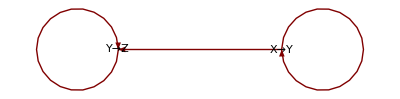

```mathematica
ShowDependencyGraph[{"X"->"Y"->"Z"->"T"},VertexLabeling->True, DirectedEdges->True]
```

#### p. 259

```mathematica
ClearAll[m,n];k Times@@FactorialPower[{10,23},{3,2}]
```

# Inverse

## Figures

#### Fig. 11.1

```mathematica
ClearAll[sol];sol:=First[ReplaceAll@@Concentrations[{0⇔X},{0.33,0.72},{0.2},{0,20}]]
```

```mathematica
times=N[Range[0,100]/5];SeedRandom[100];
data=Transpose[{times,(sol/.t->times)(1+RandomReal[{-0.025,0.025},101])}];
```

```mathematica
simdata=ListPlot[data,PlotRange->All,PlotStyle->Directive[PointSize[0.015]]]
```

```mathematica
figurexp["TothNagyPapp-Fig11.1",simdata]
```

#### Fig. 11.2

```mathematica
ClearAll[a,b,model,nlm,pl,lp,fitted];
model[a_?NumberQ,b_?NumberQ,c_?NumberQ]:=(model[a,b,c]=First[x/.NDSolve[{x'[t]==a-b x[t],x[0]==c},x,{t,20}]]);
```

```mathematica
nlm=NonlinearModelFit[data,model[a,b,c][t],{{a,.1},{b,.1},{c,1}},t];
```

```mathematica
pl=Plot[Evaluate[nlm[t]],{t,0,20},PlotRange->All,PlotStyle->Directive[Red,Thickness[0.015]],Epilog->First@simdata,ImagePadding->{{Automatic, Automatic}, {10, 10}}]
```

```mathematica
lp=ListPlot[nlm["FitResiduals"],Filling->Axis,ImagePadding->{{Automatic, Automatic}, {10, 10}}]
```

```mathematica
fitted=GraphicsRow[{pl,lp}]
```

```mathematica
figurexp["TothNagyPapp-Fig11.2",fitted]
```

```mathematica
nlm["Properties"];
```

One can also use the function Concentrations.

```mathematica
ClearAll[a,b,model2,nlm2,pl2];
model2[a_?NumberQ,b_?NumberQ,c_?NumberQ]:=(model[a,b,c]=Function[t,Evaluate[First[ReplaceAll@@Concentrations[{0⇔X},{0.33,0.72},{0.2},{0,20}]]]]);
```

```mathematica
nlm2=NonlinearModelFit[data,model2[a,b,c][t],{{a,.1},{b,.1},{c,1}},t];
```

```mathematica
pl2=Plot[Evaluate[nlm2[t]],{t,0,20},PlotRange->All,PlotStyle->Directive[Red,Thickness[0.015]],Epilog->First@simdata,ImagePadding->{{Automatic, Automatic}, {10, 10}}]
```

```mathematica
GraphicsRow[{pl2,lp}]
```

#### Fig. 11.3

```mathematica
craciunpantea1={"A_0" -> 2"A_2","A_0" -> 2"A_1","A_0" -> "A_1" +"A_2"};
```

```mathematica
cp1=ShowFHJGraph[craciunpantea1,Style[#,Bold,12]&/@{3,3,3}]
```

```mathematica
figurexp["TothNagyPapp-Fig11.3A",cp1]
```

```mathematica
cp2=ShowFHJGraph[craciunpantea1,Style[#,Bold,12]&/@{4,4,1}]
```

```mathematica
figurexp["TothNagyPapp-Fig11.3B",cp2]
```

#### Fig. 11.4

```mathematica
dyneqsteps1={Subscript[X, 1] ⇌ 2 Subscript[X, 1] + Subscript[X, 2], 2 Subscript[X, 2]⇌3 Subscript[X, 1] + Subscript[X, 2]};
dyneq1=ShowFHJGraph[dyneqsteps1,Style[#,Bold,12]&/@{1,2,3,2}]
```

```mathematica
figurexp["TothNagyPapp-Fig11.4A",dyneq1]
```

```mathematica
dyneqsteps2={Subscript[X, 1] ⇌ 2 Subscript[X, 1] + Subscript[X, 2] -> 2 Subscript[X, 2]⇌3 Subscript[X, 1] + Subscript[X, 2] ←  2 Subscript[X, 1] + Subscript[X, 2]};
dyneq2=ShowFHJGraph[dyneqsteps2,Style[#,Bold,12]&/@{1,3,1,3,2,3}]
```

```mathematica
figurexp["TothNagyPapp-Fig11.4B",dyneq2]
```

#### Fig. 11.5

```mathematica
szeder1={2 Subscript[A, 1] -> Subscript[A, 2],2 Subscript[A, 1] -> Subscript[A, 1]+Subscript[A, 2],2 Subscript[A, 1] -> 3 Subscript[A, 1],2 Subscript[A, 1] -> 2 Subscript[A, 1]+Subscript[A, 2]};
```

```mathematica
s1=ShowFHJGraph[szeder1,Array[1&,4],DirectedEdges->True,VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig11.5A",s1]
```

```mathematica
szeder2={2 Subscript[A, 1] -> Subscript[A, 2],2 Subscript[A, 1] -> Subscript[A, 1]+Subscript[A, 2],2 Subscript[A, 1] -> 3 Subscript[A, 1],2 Subscript[A, 1] -> 2 Subscript[A, 1]+Subscript[A, 2],Subscript[A, 1]+Subscript[A, 2]->Subscript[A, 2],Subscript[A, 1]+Subscript[A, 2]->2 Subscript[A, 1]+Subscript[A, 2]};
```

```mathematica
s2=ShowFHJGraph[szeder2,{1,0.1,0.1,1.9,0.1,0.1},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig11.5B",s2]
```

#### Fig. 11.6

```mathematica
origr={X+Y⇔X+2Y⇔2X+3Y-> 2Y←X+Y,2Y⇔X+2Y};
```

```mathematica
orig=ShowFHJGraph[origr,Style[#,Bold,16]&/@({"k_1","k_2","k_5","k_4","k_8","k_3","k_7","k_6"}/.{"k_1"-> 1,"k_2"-> "11/10","k_5"-> "11/10","k_4"-> 1,"k_8"-> 1,"k_3"->1 ,"k_7"-> 3,"k_6"-> "1/10"}),ImageSize->1300]
```

```mathematica
figurexp["TothNagyPapp-Fig11.6A",orig]
```

```mathematica
sparser={X+Y⇔X+2Y⇔2X+3Y-> 2Y←X+Y,2Y-> X+2Y};
```

```mathematica
sparse=ShowFHJGraph[sparser,Style[#,Bold,16]&/@({"k_1","k_2","k_3","k_4","k_5","k_6","k_7"}/.{"k_1"-> 1,"k_2"-> 1,"k_3"-> 1,"k_4"-> 1,"k_5"-> 1,"k_6"-> 1,"k_7"-> 3}),ImageSize->1000]
```

```mathematica
figurexp["TothNagyPapp-Fig11.6B",sparse]
```

```mathematica
denser={2X+3Y⇔X+Y⇔X+2Y⇔2X+3Y⇔2Y⇔X+Y,2Y⇔X+2Y};
```

```mathematica
dense=ShowFHJGraph[denser,Style[#,Bold,16]&/@({"k_1","k_2","k_3","k_4","k_5","k_6","k_7","k_8","k_9","k_10","k_11","k_12"}/.{"k_1"->"3/10","k_2"-> "3/10","k_3"->"1/10","k_4"->"11/10" ,"k_5"->"11/10","k_6"-> "1/10","k_7"-> "13/10","k_8"->"29/30" ,"k_9"->"29/30" ,"k_10"->"13/10" ,"k_11"-> "1/10","k_12"->"1/10"}),ImageSize->800]
```

```mathematica
figurexp["TothNagyPapp-Fig11.6C",dense]
```

## Calculations

#### 11.5 Identifiablility and Uniqueness Questions

```mathematica
craciunpantea1={"A_0" -> 2"A_2","A_0" -> 2"A_1","A_0" -> "A_1" +"A_2"};
```

```mathematica
RightHandSide[{craciunpantea1},{3,3,3}]
```

```mathematica
RightHandSide[{craciunpantea1},{4,4,1}]
```

#### Theorem 11.8

```mathematica
RightHandSide[{X + Y -> 2X, X + Y -> 2Y},{1,1}]
```

#### Example 11.13

```mathematica
RightHandSide[{Y->3X,X->3Y},{1,1},{x,y}]
```

# Programs

## Figures

#### Fig. 12.1

```mathematica
SeedRandom[500];sp1=SimulationPlot[{"X" ⇌ "Y"},{3.8,8.3},{20,10},1,Verbose->True,ImageSize->600]//Timing
```

```mathematica
SeedRandom[1];sp2=SimulationPlot[{"X" ⇌ "Y"},{3.8,8.3},{20,10},1,Verbose->True,ImageSize->600]//Timing
```

```mathematica
differentsimul=Column[Last/@{sp1,sp2}]
```

```mathematica
figurexp["TothNagyPapp-Fig12.1",differentsimul]
```

## Calculations

```mathematica
OpenReactionKineticsPalette
```

```mathematica
Names["ReactionKinetics`*"]
```

```mathematica
Information["ReactionKinetics`*"]
```

```mathematica
?Concentrations
```

```mathematica
?Simulation
```

```mathematica
?SimulationPlot
```

```mathematica
SeedRandom[1];
SimulationPlot2D[{"Lotka-Volterra"},{2,0.1,2},{10,12},10,ExternalSpecies->{"A","B"}]
```

```mathematica
Options[ShowFHJGraph]
```

```mathematica
?ShowFHJGraph
```

```mathematica
Models
```

```mathematica
Reactions
```

Or in a more complicated way, if you prefer:

```mathematica
GetReaction["Models"]
```

```mathematica
GetReaction["Models"]
```

```mathematica
iva=GetReaction["Ivanova"]
```

```mathematica
DeterministicModel[iva,{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{x,y,z}]
```

```mathematica
ShowVolpertGraph[{"Glyoxylate Cycle"},DirectedEdges->True,VertexLabeling->True,ImageSize->800,GraphLayout->"CircularEmbedding",Numbered->True]
```

```mathematica
ReactionsData[iva]["γ","deficiency","reactionsteporders","complexes"]
```

```mathematica
Through[{Normal,MatrixForm}[ReactionsData[iva]["γ"]]]
```

# Appendix

## Figures

#### Fig. 13.1

```mathematica
graphforesttreeetc=Row[Graph[#,GraphLayout->"CircularEmbedding",ImageSize->200,EdgeStyle->Thick,VertexSize->Small]&/@{{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,6<->4,2<->6},{3<->4,4<->5,6<->1,6<->4,2<->6},{3<->5,6<->1,6<->4,2<->6}},"      "]
```

```mathematica
figurexp["TothNagyPapp-Fig13.1",graphforesttreeetc]
```

## Calculations

# Solutions

## Introduction

Figures

Calculations

## Preparations

Figures

Calculations

#### Solution 2.1

```mathematica
ClearAll[x,y,p,a,m,M];dm1=DeterministicModel[{X+Y->2P,Y+A->X+P,2X->P+A,X+A->2X+2Z,X+Z->1/2X+A,M+Z->2M+Z,Z+M->1/2Y},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6],2 Subscript[k, 6]},{x,y,p,a,z,m}][[1]]
```

```mathematica
dm2=DeterministicModel[{"Turányi-Györgyi-Field"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5],Subscript[k, 6]},{x,y,p,a,z,m}][[1]]
```

```mathematica
Last/@dm1-Last/@dm2
```

#### Solution 2.4

```mathematica
robertson={"A" -> "B",2"B"->"B"+"C"->"A"+"C"};
```

```mathematica
FullForm[robertson]
```

```mathematica
TreeForm[robertson]
```

```mathematica
Union[Level[robertson,{-1}]]
```

A more precise solution (not neglecting real coeffiients) is:

```mathematica
species=Cases[Union[Level[robertson,{-1}]],Except[_Integer|_Real]]
```

Do not forget symbolic coefficents, like π:

```mathematica
Select[{2,"A","B","C",π},Not[NumericQ[#]]&]
```

```mathematica
M=Length[species]
```

```mathematica
ReactionsData[robertson]["M","species"]
```

#### Solution 2.5

```mathematica
FullForm[revlv={X↔2X,X+Y↔2Y,Y↔0}]
```

Note that the FullForm may depend on which sign you use for reversible reaction steps.

```mathematica
revlv/.LeftRightArrow[a_,b_]->{Rule[a,b],Rule[b,a]}//Flatten//Union
```

```mathematica
MapAt[Union,ReactionsData[revlv]["R","reactionsteps"],2]
```

```mathematica
ToReversible[{"Lotka-Volterra"}]
```

#### Solution 2.6

```mathematica
bimol={"A"+"B"->"C"};
α=Transpose[List[Coefficient[bimol[[1,1]],#]&/@{"A","B","C"}]]
β=Transpose[List[Coefficient[bimol[[1,2]],#]&/@{"A","B","C"}]]
```

```mathematica
ReactionsData[bimol]["α","β"]//Normal
```

#### Solution 2.7

```mathematica
ReactionsData[{"E"+"S1"⇔"ES1"⇔"ES1^*"->"E^*"+"P1","E^*"+"S2"⇔"ES2^*"⇔"ES2"->"E"+"P2"}][γ]//MatrixRank
```

## Graphs of Reactions

Figures

#### Fig. 14.1

```mathematica
wrongwr=ShowFHJGraph[{"A"->"B"->"C"->"A","C"->"D"->"E"->"F"->"D"}/.{x_String->Style[x,14,Bold]},DirectedEdges->True]
```

```mathematica
figurexp["TothNagyPapp-Fig14.1",wrongwr]
```

#### Fig. 14.2

```mathematica
glyoxylateshort={"oxaloacetate"+"acetyl-CoA"↔"citrate"↔"isocitrate"↔"succinate"+"glyoxylate","glyoxylate"+"acetyl-CoA"↔"malate"↔"oxaloacetate"};
```

```mathematica
glyox0=ShowVolpertGraph[{glyoxylateshort},DirectedEdges->True,VertexLabeling->True,ImageSize-> 800,GraphLayout->"CircularEmbedding",Numbered->True]
```

```mathematica
glyox=ShowVolpertGraph[{glyoxylateshort}/.{x_String->Style[x,16,Bold]},DirectedEdges->True,VertexLabeling->True,ImageSize-> 800,GraphLayout->"CircularEmbedding",Numbered->True]
```

```mathematica
figurexp["TothNagyPapp-Fig14.2",glyox]
```

Calculations

#### Solution 3.2

```mathematica
fhj=ReactionsData[{"Triangle"}]["fhjgraphedges"]
```

```mathematica
WeaklyReversibleQ[fhj]
```

```mathematica
tc=TransitiveClosureGraph[Graph[fhj]]
```

```mathematica
SymmetricGraphQ1[g_]:=AdjacencyMatrix[g]==Transpose[AdjacencyMatrix[g]]
```

```mathematica
SymmetricGraphQ2[g_]:=Module[{a=AdjacencyMatrix[g]},a==Transpose[a]]
```

```mathematica
SymmetricGraphQ3[g_]:=(a=AdjacencyMatrix[g];a==Transpose[a])
```

```mathematica
SymmetricGraphQ1[tc]
```

```mathematica
SymmetricGraphQ2[tc]
```

```mathematica
SymmetricGraphQ3[tc]
```

#### Solution 3.3

```mathematica
rg=Graph[ReactionsData[{"Robertson"}]["fhjgraphedges"]]
```

```mathematica
TableForm[IncidenceMatrix[rg],TableHeadings->{VertexList[rg],EdgeList[rg]},TableAlignments->Right]
```

#### Solution 3.4

```mathematica
Map[ReactionsData[#]["deficiency"]&,{{"Michaelis-Menten"},{"Lotka-Volterra"},{"Robertson"}}]
```

The result changes if external species are eliminated.

```mathematica
ReactionsData[{"Lotka-Volterra"},{"A","B"}]["deficiency"]
```

#### Solution 3.7

```mathematica
ReactionsData[{#}]["deficiency"]&/@{{0->X->2X},{X->Z+X,Y->Z+Y},{X->2X}}
```

#### Solution 3.8

### 1.

```mathematica
complexes[reaction_]:=Union@Flatten[ReplaceAll[h_[x___]->List[x]]/@reaction]
```

```mathematica
Ν[reaction_]:=Length[complexes[reaction]]
```

```mathematica
Sort/@{complexes[GetReaction["Lotka-Volterra"]],ReactionsData[{"Lotka-Volterra"}]["complexes"]}
```

How to show that they are identical? First possibility:

```mathematica
symmetricDifference[A_,B_]:=Union[Complement[A,B],Complement[B,A]]
```

```mathematica
symmetricDifference[complexes[GetReaction["Lotka-Volterra"]],ReactionsData[{"Lotka-Volterra"}]["complexes"]]
```

Second possibility :

```mathematica
Equal@@Sort/@{complexes[GetReaction["Lotka-Volterra"]],ReactionsData[{"Lotka-Volterra"}]["complexes"]}
```

### 2.

```mathematica
GraphPlot[{"A"+"X"->2 "X","X"+"Y"->2 "Y","Y"->"B"},DirectedEdges->True,VertexLabeling->True]
```

### 3.

```mathematica
ClearAll[α];
α:={{1,1,0},{0,1,1}}
Graph[DeleteCases[Flatten[Table[If[α[[m,r]]≠0,Labeled[DirectedEdge[X[m],r],α[[m,r]]]],{m,2},{r,3}]],Null],VertexLabels->"Name"]
```

### 4.

```mathematica
Length[WeaklyConnectedComponents[Graph[{"A"+"X"->2"X","X"+"Y"->2"Y","B"->"Y"}]]]
```

```mathematica
ReactionsData[{"A"+"X"->2"X","X"+"Y"->2"Y","B"->"Y"}]["fhjweaklyconnectedcomponents"]//Length
```

```mathematica
ReactionsData[{"A"+"X"->2"X","X"+"Y"->2"Y","B"->"Y"},{"A","B"}]["fhjweaklyconnectedcomponents"]//Length
```

#### Solution 3.9

See among the Figures.

#### Solution 3.10

```mathematica
Row@VolpertIndexing[{"Cl_2"->2"Cl^*","CH_4"+"Cl^*"->"*CH_3"+"HCl","*CH_3"+"Cl_2"->"CH_3Cl"+"Cl^*"},{"Cl_2","CH_4"},Verbose->True]
```

#### Solution 3.11

```mathematica
Row@VolpertIndexing[{"Cl_2"->2"Cl^*","CH_4"+"Cl^*"->"*CH_3"+"HCl","*CH_3"+"Cl_2"->"CH_3Cl"+"Cl^*"},{"Cl^*","CH_4"},Verbose->True]
```

#### Solution 3.14

```mathematica
AcyclicGraphQ[Graph[{X->Y,X+Y->Z}]]
```

```mathematica
AcyclicVolpertGraphQ[{X->Y,X+Y->Z}]
```

## Mass conservation

Figures

Calculations

#### Solution 4.3

```mathematica
MQ[gamma_,m_,r_]:=Quiet[First[Maximize[{lambda,Transpose[gamma].Array[rho[#]&,m]==ConstantArray[0,r],Thread[Array[rho[#]&,m]≥lambda ConstantArray[1,m]],Array[rho[#]&,m].ConstantArray[1,m]==1},Join[Array[rho[#]&,m],{lambda}]]]>0];
```

Let us try the function on the given examples.

```mathematica
reac1={"A"+"B"⇔"C"->2"D"⇔"B"+"E"};
```

```mathematica
ex1={γ1,m1,r1}=ReactionsData[reac1][γ,"M","R"]
```

```mathematica
MQ@@ex1
```

```mathematica
m1-MatrixRank[γ1]
```

```mathematica
{m1,MatrixRank[γ1]}
```

```mathematica
MassConservationRelations[{reac1}]
```

```mathematica
GammaLeftNullSpace[{reac1}]
```

```mathematica
FindInstance[MassConservationRelations[reac1],ReactionsData[reac1]["variables"]/.c->ρ,Integers]
```

```mathematica
reac2={"A"->2"M"+"N2","A"+"M"->"CH4"+"B",2"M"->"C2H6","M"+"B"->"MED","M"+"A"->"C","M"+"C"->"TMH"};
```

```mathematica
ex2={γ2,m2,r2}=ReactionsData[reac2][γ,"M","R"]
```

```mathematica
Column[{MQ@@ex2,m2-MatrixRank[γ2],{m2,MatrixRank[γ2]},MassConservationRelations[{reac2}],FindInstance[MassConservationRelations[reac2],ReactionsData[reac2]["variables"]/.c->ρ,Integers]}]
```

An alternative solution may give simpler solutions for the mass vector.

```mathematica
FindInstance[Join[Thread[Array[ρ[#]&,m1].ReactionsData[reac1][γ]==0],Thread[Array[ρ[#]&,m1]>0]],Array[ρ[#]&,m1],Integers]
```

```mathematica
FindInstance[Join[Thread[Array[ρ[#]&,m2].ReactionsData[reac2][γ]==0],Thread[Array[ρ[#]&,m2]>0]],Array[ρ[#]&,m2],Integers]
```

## Decompositions

Figures

Calculations

#### Solution 5.2

```mathematica
MLD[M_]:=Length[#]==1&&Min[Abs[#[[1]]]]>0&[NullSpace[Transpose[M]]]
```

```mathematica
Z={{1,0,1,0,2,2},{0,2,1,1,0,1}};
```

```mathematica
MatrixForm[Transpose[Z]]
```

```mathematica
r=Rest[Subsets[Transpose[Z]]];
```

```mathematica
Column/@(sel=Select[r,MLD[#]&])
```

#### Solution 5.3

```mathematica
DependenceType[A_,set_]:=Switch[NullSpace[Transpose[A⟦set⟧]],{},"I",_?(Length[#]≥2||Min[Abs[#]]==0&),"D",_,"S"]
```

```mathematica
DependenceType[Transpose[Z],{2,3}]
```

```mathematica
DependenceType[Transpose[Z],{1,2,5}]
```

```mathematica
DependenceType[Transpose[Z],{1,2,3}]
```

```mathematica
ClearAll[MDSIter];
MDSIter[{{set_,type:("U"|"S"|"I")},A_,m_,sol_}/;set===Range[First[set],m]]:={{set,type},A,m,sol}
MDSIter[{{set_,"D"},A_,m_,sol_}/;set===Range[First[set],m]]:={{Delete[set,-2],"U"},A,m,sol}
MDSIter[{{{T___,tt_,m_},type_},A_,m_,sol_}]:={{{T,tt+1},"U"},A,m,sol}
MDSIter[{{{T___,tt_},"I"},A_,m_,sol_}/;tt<m]:={{{T,tt,tt+1},"U"},A,m,sol}
MDSIter[{{{T___,tt_},"D"},A_,m_,sol_}/;tt<m]:={{{T,tt+1},"U"},A,m,sol}
MDSIter[{{{T___,tt_},"S"},A_,m_,sol_}/;tt<m]:={{{T,tt+1},"U"},A,m,sol}
MDSIter[{{set_,"U"},A_,m_,sol_}]:=(tt=DependenceType[A,set];{{set,tt},A,m,If[tt==="S",Append[sol,set],sol]})

MinimalDependentSubsets[A_]:=Last[FixedPoint[MDSIter,{{{1},"U"},A,Length[A]+1,{}}]]
```

```mathematica
Timing[mds=MinimalDependentSubsets[Transpose[Z]]]
```

```mathematica
Length[mds]
```

```mathematica
Length[sel]
```

#### Solution 5.4

```mathematica
szalkai={"CO","CO2","O2","H2","CH2O","CH3OH","C2H5OH","(CH3)2CO","CH4","CH3CHO","H2O"};
```

```mathematica
ToAtomMatrix[szalkai,FormattedOutput->True]
```

```mathematica
MatrixForm[Zszalkai=Most/@Transpose[ToAtomMatrix[szalkai][[2]]]]
```

```mathematica
Timing[t1=MLD/@Rest[Subsets[Zszalkai]];]
```

```mathematica
Count[t1,True]
```

```mathematica
Timing[t2=MinimalDependentSubsets[Zszalkai];]
```

```mathematica
Length[t2]
```

The second version is mch faster.

```mathematica
Length[MinimalDependentSubsets[Most/@Transpose[ToAtomMatrix[szalkai]⟦2⟧]]]
```

#### Solution 5.5

```mathematica
VolpertIndexing[{"H"+"O2"->"O"+"OH","O"+"OH"->"H"+"OH","OH"+"H2"->"H"+"H2O",2"H"->"H2","H"+"OH"⇔"H2O"},{"H","H2","O2"},Verbose->True]
```

#### Solution 5.6

```mathematica
ClearAll[MyOmittable1];
MyOmittable1[gamma_,b_]:=
Block[{m,r,zs,optval,optz},
{m,r}=Dimensions[gamma];
zs=Array[z,r];
1-FixedPoint[Function[χ,{optval,optz}=Minimize[{χ.zs,And@@Thread[gamma.zs==b]&&And@@Thread[zs≥0]&&χ.zs≥1},zs];
χ *(1-Boole[Thread[(zs/.optz) == 0]])],Array[1&,r]]];
```

```mathematica
ClearAll[reac,overall1,overall2,gammareac,gammaoverall1,gammaoverall2];
reac = {"X"->2"Y",3"A"->4"B"};
overall1 = {Inner[Plus,Sequence@@reac,Rule]};
overall2 = {"X"->2"Y"};
gammareac=ReactionsData[reac]["γ"]//Normal
gammaoverall1=ReactionsData[overall1]["γ"]//Normal
gammaoverall2=ReactionsData[overall2]["γ"]//Normal
```

```mathematica
MyOmittable1[{{-1,0},{2,0},{0,-3},{0,4}},{-1,2,-3,4}]
```

Neither of the reaction steps can be omitted.

```mathematica
MyOmittable1[{{-1,0},{2,0},{0,-3},{0,4}},{-1,2,0,0}]
```

In the second example the second step can be omitted.

```mathematica
ClearAll[rddecomp];
rddecomp=ReactionsData[{"H"+"O2"->"O"+"OH","O"+"H2"->"H"+"OH","OH"+"H2"->"H"+"H2O",2"H"->"H2","H"+"OH"⇔"H2O"}];
```

```mathematica
rddecomp[γ]
```

```mathematica
rddecomp["species"]
```

```mathematica
b={"H"+"O2"+3"H2"->3"H"+2"H2O"}
```

```mathematica
MyOmittable1[rddecomp[γ],{2,-1,0,0,-3,2}]
```

That is, the last three reaction steps can be omitted. And, really, we find a decomposition below only consructed from the first three reaction steps.

```mathematica
Decompositions[b,{"H"+"O2"->"O"+"OH","O"+"H2"->"H"+"OH","OH"+"H2"->"H"+"H2O"}]
```

#### Solution 5.7

```mathematica
ClearAll[reac,overall,gammareac,gammaoverall];
reac = {"X"->2"Y","A"->"B"};
overall1 = {Inner[Plus,Sequence@@reac,Rule]};
overall2 = {"X"->2"Y"};
gammareac=ReactionsData[reac]["γ"]//Normal
gammaoverall1=ReactionsData[overall1]["γ"]//Normal
gammaoverall2=ReactionsData[overall2]["γ"]//Normal
```

```mathematica
MyOmittable2[gamma_,b_]:=Complement[Range[Length[First[gamma]]],Union[Last/@Position[CoveringDecompositionSet[b,gamma],_?Positive]]];
```

```mathematica
MyOmittable2[{{-1,0},{2,0},{0,-1},{0,1}},{-1,2,-1,1}]
```

```mathematica
MyOmittable2[{{-1,0},{2,0},{0,-1},{0,1}},{-1,2,0,0}]
```

```mathematica
CoveringDecompositionSet[{-1,2,-1,1},{{-1,0},{2,0},{0,-1},{0,1}}]
```

```mathematica
CoveringDecompositionSet[{-1,2,0,0},{{-1,0},{2,0},{0,-1},{0,1}}]
```

## Induced

Figures

#### Fig. 14.3

```mathematica
lv=GetReaction["Lotka-Volterra"]
```

```mathematica
re=ReactionsData[lv,ExternalSpecies->{"A","B"}]["fhjgraphedges"]
```

```mathematica
small=ReplaceAll@@Concentrations[{re},{1,1,1},{2,3},{0,20},{x,y}];
```

```mathematica
large=ReplaceAll@@Concentrations[{re},{1,1,1},{4,5},{0,20},{x,y}];
```

```mathematica
lvtwocurves1=ParametricPlot[Evaluate[{small,large}],{t,0,20},PlotRange->All,PlotStyle->Directive[Thickness[0.01]],PlotLegends->{"smaller\ninitial\nvalue","larger\ninitial\nvalue"},Epilog->{PointSize[Large], Point[{2,3}],Point[{4,5}]}]
```

```mathematica
figurexp["TothNagyPapp-Fig14.3",lvtwocurves1]
```

#### Fig. 14.4

```mathematica
lvtwocurves2=Plot[Evaluate[{small-large}],{t,0,20},PlotRange->All,PlotStyle->Directive[Thickness[0.01]],PlotLegends->{"Δx","Δy"}]
```

```mathematica
figurexp["TothNagyPapp-Fig14.4",lvtwocurves2]
```

#### Fig. 14.5

```mathematica
gOH=Graph[{Labeled[1,Style["HCOOH",Bold,16]],Labeled[2,Style["H_2O",SingleLetterItalics->False,Bold,16]],Labeled[3,Style["CH_3OH",Bold,16]]},{Labeled[1->2,Style["1/2 w(c(t))",Bold,16]],Labeled[3->2,Style["1/2 w(c(t))",Bold,16]]},VertexLabels->"Name",VertexSize->Small,ImageSize->500,ImagePadding->50,GraphLayout->"LinearEmbedding"]
```

```mathematica
figurexp["TothNagyPapp-Fig14.5",gOH]
```

#### Fig. 14.6

```mathematica
gHrev=GraphPlot[{{"H"->"OH","w_1/2+w_-3/6"},{"OH"->"H","w_-1/2+w_3/6"},{"H_2"->"H","2w_2/4+2w_3/6"},{"H"->"H_2","2w_-2/4+2w_-3/6"},
{"H_2"->"H_2O","4w_3/6"},{"H_2O"->"H_2","4w_-3/6"},
{"H_2"->"OH","2w_2/4"},{"OH"->"H_2","2w_-2/4"},
{"H_2O"->"OH","2w_-3/6"},{"OH"->"H_2O","2w_3/6"}}/.{x_String->Style[x,SingleLetterItalics->False,16,Bold]},DirectedEdges->True,VertexLabeling->True,ImageSize->1600]
```

```mathematica
figurexp["TothNagyPapp-Fig14.6A",gHrev]
```

```mathematica
gOrev=GraphPlot[{{"O_2"->"OH","2w_1/4\n"},{"OH"->"O_2","\n2w_-1/4\n\n"},
{"O_2"->"O","2w_1/4"},{"O"->"O_2","\n\n2w_-1/4"},
{"O"->"OH","w_2/2"},{"OH"->"O","w_-2/2"},
{"OH"->"H_2O","w_3/2"},{"H_2O"->"OH","w_-3/2"}}/.{x_String->Style[x,SingleLetterItalics->False,16,Bold]},DirectedEdges->True,VertexLabeling->True,ImageSize->600]
```

```mathematica
figurexp["TothNagyPapp-Fig14.6B",gOrev]
```

#### Fig. 14.7

```mathematica
ndstemp=ParametricNDSolve[{c'[t]==10^(-1000/T[t]) c[t],T'[t]==-Q 10^(-1000/T[t])c[t],c[0]==1,T[0]==300},{c,T},{t,0,10000},{Q}];
```

```mathematica
mult1=300;exocT=Plot[Evaluate[{mult1 c[-100][t],T[-100][t]}/.ndstemp],{t,0,500},PlotStyle->{Directive[{Thick,Red}],Directive[{Thick,Blue}]},PlotRange->All,AxesLabel->{Style["t",Italic,Bold,16],Style[ToString[mult1]<>"c(t),T(t)",Italic,Bold,16]},PlotLegends->Placed[{ToString[mult1]<>"c","T"},Above]]
```

```mathematica
figurexp["TothNagyPapp-Fig14.7A",exocT]
```

```mathematica
mult=300;endocT=Plot[Evaluate[{mult c[600][t],T[600][t]}/.ndstemp],{t,0,500},PlotStyle->{Directive[{Thick,Red}],Directive[{Thick,Blue}]},PlotRange->All,AxesLabel->{Style["t",Italic,Bold,16],Style[ToString[mult]<>"c(t),T(t)",Italic,Bold,16]},PlotLegends->Placed[{ToString[mult]<>"c","T"},Above]]
```

```mathematica
figurexp["TothNagyPapp-Fig14.7B",endocT]
```

Calculations

#### Solution 6.4

```mathematica
ClearAll[Y,r];{Y,r}=ReactionsData[{"Lotka-Volterra"},{"A","B"}]["complexes","fhjgraphedges"]
```

```mathematica
TableForm[Boole[Outer[SameQ,Y,Last/@r]]-Boole[Outer[SameQ,Y,First/@r]],
TableHeadings->{Y,r},
TableAlignments->{Right,Top}]
```

Shorter, but less easy to read.

```mathematica
TableForm[Subtract@@(Boole[Outer[SameQ,Y,#/@r]]&/@{Last,First}),
TableHeadings->{Y,r},
TableAlignments->{Right,Top}]
```

```mathematica
TeXForm[TableForm[Boole[Outer[SameQ,Y,Last/@r]]-Boole[Outer[SameQ,Y,First/@r]]]]
```

A very short solution using the built-in function IncidenceMatrix of Mathematica.

```mathematica
TableForm[IncidenceMatrix[Graph[r]],TableHeadings->{Y,r},TableAlignments->Right]
```

#### Solution 6.6

```mathematica
ClearAll[Y,r];Y=ReactionsData[{"Michaelis-Menten"}]["complexes"]
```

```mathematica
r=ReactionsData[{"Michaelis-Menten"}]["fhjgraphedges"]
```

A version different from that given as solution to Problem 6.4 above follows.

```mathematica
gg[a_,b_]:=Which[a===b[[1]],-1,a===b[[2]],1,True,0]
```

```mathematica
TableForm[Outer[gg,Y,r],TableHeadings->{Y,r},TableAlignments->{Right,Top}]
```

```mathematica
TeXForm[TableForm[Outer[gg,Y,r]]]
```

```mathematica
TableForm[IncidenceMatrix[Graph[r]],TableHeadings->{Y,r},TableAlignments->Right]
```

#### Solution 6.7

```mathematica
mole=GetReaction["Mole"]
```

```mathematica
Times@@@(Power[{x,y},#]&/@Union@Flatten[Transpose/@ReactionsData[{mole}]["α","β"],1])
```

#### Solution 6.9

```mathematica
ClearAll[A,G,α,γ]
G[α_,γ_]:=γ.DiagonalMatrix[Times@@({x,y}^α)]
```

```mathematica
G@@Normal[ReactionsData[{"Mole"}]["α","γ"]]
```

```mathematica
%.{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],k}
```

```mathematica
RightHandSide[{"Mole"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],k},{x,y}]
```

#### Solution 6.10

```mathematica
ClearAll[b,a,e,f];Factor/@RightHandSide[{"X"+"Y"-> 2"X"-> "X"-> 0 ←"Y" ← 2"Y"},{c,b,a,e,f},{x,y}]
```

#### Solution 6.11

```mathematica
ClearAll[Y,x,y];DeterministicModel[{2X+Y->X+2Y},{1},{x,y}]
```

#### Solution 6.12

```mathematica
ReplaceAll@@Concentrations[{"A"->"B"->"C"},{1,1},{a0,b0,c0},{a,b,c},t]/.{a0->Subscript[a, 0],b0->Subscript[b, 0],c0->Subscript[c, 0]}
```

#### Solution 6.15

```mathematica
ClearAll[x,y,eq];
eq=DeterministicModel[{2X->3X},{1},{x}][[1,1]]
```

```mathematica
x[t_]:=Subscript[x, 0]+Sum[Subscript[c, k]/(k!)t^k,{k,5}]+O[t]^6
```

```mathematica
x[t]/.First@Solve@LogicalExpand[eq]
```

```mathematica
ClearAll[x];ReplaceAll@@Concentrations[{2X->3X},{1},{x0},{x},t]//Simplify
```

#### Solution 6.18

```mathematica
?*Atom*
```

```mathematica
AtomConservingQ[{"HCOOH"+"CH3OH"->"HCOOCH3"+"H2O"}]
```

#### Solution 6.22

See Fig. 14.7

## Stationary

Figures

Calculations

#### Solution 7.1

```mathematica
ClearAll[gb];Column[gb=GroebnerBasis[poly={x(1-2x+3y+z),y(1+3x-2y+z),z(2+y-z)},{x,y,z}]]
```

```mathematica
TeXForm[gb]
```

```mathematica
TeXForm@TableForm[{x,y,z}/.Solve[{x(1-2x+3y+z)==0,y(1+3x-2y+z)==0,z(2+y-z)==0},{x,y,z}],TableHeadings->{{},{"x","y","z"}}]
```

```mathematica
Reduce[{x(1-2x+3y+z)==0,y(1+3x-2y+z)==0,z(2+y-z)==0},{x,y,z}]
```

#### Solution 7.3

```mathematica
Factor/@DeterministicModel[{"Horn-Jackson"},{ϵ,1,ϵ,1},{x,y}][[1]]
```

```mathematica
Solve[((2 ϵ x[t]^2-x[t] y[t]+2 ϵ x[t] y[t]+2 ϵ y[t]^2)/.{ϵ->1/12})==0,y[t]]
```

```mathematica
stat=Solve[2 ϵ x^2-x y+2 ϵ x y+2 ϵ y^2==0,y]
```

```mathematica
ev=EigensystemJacobian[{"Horn-Jackson"},{ϵ,1,ϵ,1},{x,y}]/.stat
```

See also Fig. 7.3

#### Solution 7.4

```mathematica
ClearAll[Z];Rest@StationaryPoints[{X+Y->U,Y+Z->V},{k1,k2},{x0,y0,0,z0,0},{x,y,u,z,v}]//TableForm
```

#### Solution 7.7

```mathematica
{"A"⇌"B",2 "A"⇌2"B"}
```

```mathematica
DeterministicModel[{"A"⇌"B",2 "A"⇌2"B"},{("A")^2,"B","A",("B")^2},{x,y},MassAction->False]
```

```mathematica
RightHandSide[{"A"⇌"B",2 "A"⇌2"B"},{("A")^2,"B","A",("B")^2},{x,y},MassAction->False]
```

```mathematica
StationaryPoints[{"A"⇌"B",2 "A"⇌2"B"},{("A")^2,"B","A",("B")^2},{x0,y0},{SubStar[x],SubStar[y]},MassAction->False]
```

#### Solution 7.8

```mathematica
ψ[x_,y_,u_,z_,v_]:=x^Subscript[k, 2]/z^Subscript[k, 1]
```

```mathematica
rh=RightHandSide[{X+Y->U,Y+Z->V},{Subscript[k, 1],Subscript[k, 2]},{x,y,u,z,v}]
```

```mathematica
D[ψ[x,y,u,z,v],{{x,y,u,z,v},1}].rh
```

```mathematica
MatrixRank[{{1,0,0,1,0},{0,1,0,1,1},{0,0,1,0,1},D[ψ[x,y,u,z,v],{{x,y,u,z,v},1}]}]
```

#### Solution 7.9

```mathematica
StationaryPoints[{X⇔0},{k1,k2},{x0},{SubStar[x]}]
```

#### Solution 7.11

```mathematica
Concentrations[ToReversible["Triangle"],Array[k[#],6],{a0,b0,c0}]
```

#### Solution 7.12

```mathematica
DeterministicModel[{"Wegscheider"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4]},{a,b}]
```

#### Solution 7.13

```mathematica
RightHandSide[{3Y->3X->2X+Y},{1,1/2},{x,y}]
```

```mathematica
RightHandSide[{3Y⇔3X},{1,1/2},{x,y}]
```

#### Solution 7.14

```mathematica
StationaryPoints[{"Lotka-Volterra"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{x0,y0},{SubStar[x],SubStar[y]},ExternalSpecies->{"A","B"}]
```

```mathematica
olv=Solve[D[Subscript[k, 3] Log[x]+Subscript[k, 1] Log[y]-Subscript[k, 2] x-Subscript[k, 2] y,{{x,y},1}]==0,{x,y}][[1]]
```

```mathematica
D[Subscript[k, 3] Log[x]+Subscript[k, 1] Log[y]-Subscript[k, 2] x-Subscript[k, 2] y,{{x,y},2}]/.olv
```

```mathematica
D[Subscript[k, 3] Log[x]+Subscript[k, 1] Log[y]-Subscript[k, 2] x-Subscript[k, 2] y,{{x,y},2}]/.olv
```

#### Solution 7.15

```mathematica
rs=RightHandSide[{"Ivanova"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{x,y,z}]
```

```mathematica
ψ[x_,y_,z_]:=x+y+z;
φ[x_,y_,z_]:=x^Subscript[k, 2] y^Subscript[k, 3] z^Subscript[k, 1];
```

```mathematica
D[ψ[x,y,z],{{x,y,z},1}].rs
```

```mathematica
D[φ[x,y,z],{{x,y,z},1}].rs//Simplify
```

#### Solution 7.16

```mathematica
AbsoluteConcentrationRobustness[{"Lotka-Volterra"},ExternalSpecies->{"A","B"}]
```

#### Solution 7.18

```mathematica
Options[AbsoluteConcentrationRobustness]
```

```mathematica
(*AbsoluteConcentrationRobustness[{"E"+"I_p"↔"EI_p"->"E"+"I","EI_p"+"I"↔"EI_pI"->"EI_p"+"I_p"},TimeLimit->600]*)
```

Cf. also with Fig. 7.8

```mathematica
ClearAll[a,b,d,e];rihs=RightHandSide[{"E"+"I_p"↔"EI_p"->"E"+"I","EI_p"+"I"↔"EI_pI"->"EI_p"+"I_p"},{Subscript[k, 1],Subscript[k, -1],Subscript[k, 2],Subscript[k, 3],Subscript[k, -3],Subscript[k, 4]},{a,b,c,d,e}]
```

```mathematica
?MassConservationRelations
```

```mathematica
MassConservationRelations[{"E"+"I_p"↔"EI_p"->"E"+"I","EI_p"+"I"↔"EI_pI"->"EI_p"+"I_p"},{a,b,c,d,e}]
```

```mathematica
rihs/.{b->(Subscript[k, -1]+Subscript[k, 2])/(a Subscript[k, 1])c,e->Subscript[k, 2]/Subscript[k, 4] c,d-> Subscript[k, 2]/Subscript[k, 3]}//Simplify
```

#### Solution 7.19

```mathematica
ClearAll[lilipota,f2,y0,f,XX,x];lilipota[f2_,y0_,f_]:=f x^3-f x^2+x(f^2+(f-f2)y0)-f^2;
Manipulate[ParametricPlot[(XX[f2_,y0_,φ_]:=x/.NSolve[lilipota[f2,y0,10^φ]==0,{x}];
Distribute[{φ,XX[f2,y0,φ]},List]),{φ,-3,-1},PlotRange->{{-3,-1},{0,1.2}}],{{f2,1/135},0.0009,0.0075,0.0001},{{y0,10/27},0.24,0.38,0.01}]
```

## Transient

Figures

#### Fig. 14.8

```mathematica
a=1;b=2.5;
sp=StreamPlot[{1-x-b x+a x^2 y,b x-a x^2 y},{x,0,20},{y,0,10}]
```

```mathematica
cp=ContourPlot[{1-x-b x+a x^2 y==0,b x-a x^2 y==0},{x,0,20},{y,0,10},ContourStyle->{{Thick,Red},{Thick,Dashed,Blue}}]
```

```mathematica
x0=10.5;brusselatorBendixson=Show[sp,cp,Graphics[{Thick,Line[{{1/(b+1),0},{1/(b+1),(b(b+1))/a},{2,(b(b+1))/a},{x0,2-x0+(b(b+1))/a},{x0,0},{1/(b+1),0}}],PointSize->Medium,Point[{1,b/a}],Circle[{1,b/a},0.3],Text[Style["ẋ = 0",Bold,Medium,Red],{5,1}],Text[Style["ẏ = 0",Bold,Medium,Blue],{1,5}]}],AspectRatio->Automatic,PlotRange->{{0,12},{0,10}}]
```

```mathematica
figurexp["TothNagyPapp-Fig14.8",brusselatorBendixson]
```

#### Fig. 14.9

```mathematica
parabola=RegionPlot[((a+b)Subscript[k, 2]-Subscript[k, 1] Subscript[k, 3])^2≥4b Subscript[k, 1] Subscript[k, 2] Subscript[k, 3]/.{Subscript[k, 1]->1,Subscript[k, 2]->1,Subscript[k, 3]->1},{a,-3,3},{b,-1,3}]
```

```mathematica
figurexp["TothNagyPapp-Fig14.9",parabola]
```

#### Fig. 14.10

```mathematica
p1=RegionPlot[(a+b)/(Subscript[k, 3]-Subscript[k, 2])≥0/.{Subscript[k, 1]->1,Subscript[k, 2]->2,Subscript[k, 3]->3},{a,-3,3},{b,-1,3},PlotLabel->Row[{"k_1=1, k_2=2, k_3=3"}]]
```

```mathematica
figurexp["TothNagyPapp-Fig14.10A",p1]
```

```mathematica
p2=RegionPlot[(a+b)/(Subscript[k, 3]-Subscript[k, 2])≥0/.{Subscript[k, 1]->1,Subscript[k, 2]->3,Subscript[k, 3]->2},{a,-3,3},{b,-1,3},PlotLabel->Row[{"k_1=1, k_2=3, k_3=2"}]]
```

```mathematica
figurexp["TothNagyPapp-Fig14.10B",p2]
```

#### Fig. 14.11

```mathematica
/.x_Integer->Style[x,Bold,12]
```

```mathematica
complexgraphslotkavolterra=GraphicsRow[GraphPlot[#,VertexLabeling->True]&/@{{0->0},{1->0},{2->1},{2->2},{2->0}},ImageSize->Large]
```

```mathematica
figurexp["TothNagyPapp-Fig14.11",complexgraphslotkavolterra]
```

#### Fig. 14.12

```mathematica
complexgraphlotkavolterra=GraphPlot[{0->1,0->0,2->2,1->2,
1->1},VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig14.12",complexgraphlotkavolterra]
```

#### Fig. 14.13

```mathematica
nflux=GraphPlot[{{Style["N_2O_5",Italic]->Style["NO_2",Italic],1/2},{Style["N_2O_5",Italic]->Style["NO_3",Italic],1/2},
{Style["NO_2",Italic]->Style["N_2O_5",Italic],1/2},{Style["NO_2",Italic]->Style["NO",Italic],1/4},{Style["NO_2",Italic]->Style["NO_2",Italic],1},{Style["NO_3",Italic]->Style["N_2O_5",Italic],1/2},{Style["NO_3",Italic]->Style["NO_2",Italic],3/4},{Style["NO_3",Italic]->Style["NO",Italic],1/2},{Style["NO",Italic]->Style["NO_2",Italic],1}},DirectedEdges->True,EdgeRenderingFunction->({Thickness[0.01*#3],Red,Arrowheads->0.07,Arrow[#1]}&),VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig14.13A",nflux]
```

```mathematica
oflux=GraphPlot[{{Style["N_2O_5",Italic]->Style["NO_2",Italic],1},{Style["N_2O_5",Italic]->Style["NO_3",Italic],3/2},

{Style["NO_2",Italic]->Style["N_2O_5",Italic],1},
{Style["NO_2",Italic]->Style["NO_2",Italic],2/5},
{Style["NO_2",Italic]->Style["NO",Italic],1/5},{Style["NO_2",Italic]->Style["O_2",Italic],2/5},

{Style["NO_3",Italic]->Style["N_2O_5",Italic],3/5},{Style["NO_3",Italic]->Style["NO_2",Italic],21/10},{Style["NO_3",Italic]->Style["NO",Italic],3/10},{Style["NO",Italic]->Style["NO_2",Italic],3/5}},DirectedEdges->True,EdgeRenderingFunction->({Thickness[0.01*#3],Red,Arrowheads->0.07,Arrow[#1]}&),VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig14.13B",oflux]
```

#### Fig. 14.14

```mathematica
DeterministicModel[{"Lotka-Volterra"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]},{x,y},ExternalSpecies->{"A","B"}]
```

```mathematica
ClearAll[inf];inf[pm1_,pm2_,pm3_,pm4_]:=GraphPlot[{{"X"->"X","   "<>pm1},{"X"->"Y","\n"<>pm2},{"Y"->"X",pm3<>"\n"},{"Y"->"Y",pm4<>"   "}}/.x_String->Style[x,Bold,16],DirectedEdges->True,VertexLabeling->True,EdgeLabeling->True,ImageSize->400];
```

```mathematica
influLL=inf["+","+","-","-"];
influRL=inf["+","+","-","+"];
influLU=inf["-","+","-","-"];
influRU=inf["-","+","-","+"];
influ=Grid[{{influLL,influRL},{influLU,influRU}}]
```

```mathematica
figurexp["TothNagyPapp-Fig14.14",influ]
```

Calculations

#### Solution 8.3

#### Solution 8.9

```mathematica
ClearAll[Y,x0,y0];
DeterministicModel[{X->Y->4X},{1,1},{x,y}]
con=ReplaceAll@@Concentrations[{X->Y->4X},{1,1},{Subscript[x, 0],Subscript[y, 0]},t]
```

```mathematica
Limit[con,t->+∞]
```

```mathematica
StationaryPoints[{X->Y->4X},{1,1},{x0,y0}]
```

```mathematica
ReactionsData[{X->Y->4X}]["deficiency"]
```

#### Solution 8.12

```mathematica
Solve[Array[Subscript[ρ, #]&,3].ReactionsData[{Z←X->Y,Y+Z->2X}]["γ"]==0,Array[Subscript[ρ, #]&,3]]
```

```mathematica
GammaLeftNullSpace[{"Z"←"X"->"Y","Y"+"Z"->2"X"}]
```

```mathematica
dm=DeterministicModel[{Z←X->Y,Y+Z->2X},{k,1,1},{x,y,z}][[1]]
```

```mathematica
sa=SolveAlways[Expand[{a,b,c}.RightHandSide[{Z←X->Y,Y+Z->2X},{k,1,1},{x,y,z}]]==0,{x,y,z}]
```

```mathematica
sa[[1]]/.{a->2,b->1}
```

#### Solution 8.13

```mathematica
ReactionsData[ToReversible["Lotka-Volterra"],{"A","B"}]["deficiency"]
```

```mathematica
DetailedBalanced[ToReversible["Lotka-Volterra"],{Subscript[k, 1],Subscript[k, -1],Subscript[k, 2],Subscript[k, -2],Subscript[k, -3],Subscript[k, 3]},ExternalSpecies->{"A","B"}]
```

```mathematica
rhs=RightHandSide[ToReversible["Lotka-Volterra"],{Subscript[k, 1],Subscript[k, -1],Subscript[k, 2],Subscript[k, -2],Subscript[k, -3],Subscript[k, 3]},{x,y},ExternalSpecies->{"A","B"}]
```

```mathematica
FullSimplify[Subscript[k, 2] Subscript[k, 1]/Subscript[k, -1] Subscript[k, -3]/Subscript[k, 3]==Subscript[k, -2] Subscript[k, -3]^2/Subscript[k, 3]^2,Assumptions->Thread[{Subscript[k, 1],Subscript[k, -1],Subscript[k, 2],Subscript[k, -2],Subscript[k, -3],Subscript[k, 3]}>0]]
```

#### Solution 8.14

```mathematica
ClearAll[dm,a,b];dm=DeterministicModel[{"P"->"A","A"+2"B"->3"B","B"->"C"},{Subscript[k, 1] p,Subscript[k, 2],Subscript[k, 3]},{a,b},ExternalSpecies->{"P","C"}][[1]]
```

```mathematica
RightHandSide[{"P"->"A","A"+2"B"->3"B","B"->"C"},{Subscript[k, 1] p,Subscript[k, 2],Subscript[k, 3]},{x,y},ExternalSpecies->{"P","C"}]/.{Subscript[k, 1]->μ/p,Subscript[k, 2]->1,Subscript[k, 3]->1}
```

```mathematica
evj=EigensystemJacobian[{"P"->"A","A"+2"B"->3"B","B"->"C"},{μ/p,1,1},{a,b},ExternalSpecies->{"P","C"}]/.{a->1/μ,b->μ}
```

```mathematica
Simplify[{SubMinus[λ][μ],SubPlus[λ][μ]}=evj[[1]]]
```

```mathematica
Solve[1-6 μ^2+μ^4==0]
```

```mathematica
Plot[1-6 μ^2+μ^4,{μ,-3,3}]
```

```mathematica
{SubMinus[λ][μ],SubPlus[λ][μ]}/.μ->1
```

```mathematica
D[{SubMinus[λ][μ],SubPlus[λ][μ]},μ]/.μ->1
```

```mathematica
ff[x_,y_]:={-x y^2+μ,-y+x y^2}
```

```mathematica
ff[x,y][[1]]
```

```mathematica
1/16(D[ff[x,y][[1]],{x,3}]+D[ff[x,y][[1]],{x,1},{y,2}]+D[ff[x,y][[2]],{x,2},{y,1}]+D[ff[x,y][[2]],{y,3}])+1/(16 1)(D[ff[x,y][[1]],{x,1},{y,1}](D[ff[x,y][[1]],{x,2}]+D[ff[x,y][[1]],{y,2}]))
```

#### Solution 8.15

```mathematica
nos=GetReaction[{"Explodator"}]/.{aExplodator->Subscript[β, 1]-1,bExplodator->Subscript[β, 2]-1}
```

```mathematica
rhs=RightHandSide[{nos},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4]},{x,y,z},ExternalSpecies->{"A","P"}]
```

```mathematica
sp=StationaryPoints[{nos},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4]},{x0,y0,z0},{x,y,z},ExternalSpecies->{"A","P"}]
```

```mathematica
stp=sp[[2,2]]//Simplify
```

```mathematica
ejm0=EigensystemJacobian[{nos},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4]},{x,y,z},ExternalSpecies->{"A","P"}][[1]]/.{x->0,y->0,z->0}//ToRadicals
```

```mathematica
stp[[{3,4,5}]]
```

```mathematica
ejm1=EigensystemJacobian[{nos},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4]},{x,y,z},ExternalSpecies->{"A","P"}][[1]]/.stp[[{3,4,5}]]
```

```mathematica
MatrixForm[jac=D[rhs,{{x,y,z},1}]]
```

```mathematica
jac/.{x->0,y->0,z->0}//MatrixForm
```

```mathematica
jac/.stp[[{3,4,5}]]//MatrixForm
```

```mathematica
Tr[jac/.stp[[{3,4,5}]]]//FullSimplify
```

```mathematica
Det[jac/.stp[[{3,4,5}]]]//FullSimplify
```

```mathematica
Collect[CharacteristicPolynomial[jac/.stp[[{3,4,5}]],x]//FullSimplify,x]
```

#### Solution 8.16

```mathematica
vichaos={"A"+"B"->2"B","B"+"C"->2"C","C"+"A"->2"A","A"+"D"->2"D","D"+"E"->2"E","E"+"A"->2"A"};
```

```mathematica
ReactionsData[{vichaos}]["species","reactionsteps"]
```

```mathematica
(spvi=StationaryPoints[{vichaos},{100,660,600,100,660,360},{1,2,3,4,5},{aa,bb,cc,dd,ee}][[2]])//Column
```

```mathematica
spvi[[7]]
```

```mathematica
D[RightHandSide[{vichaos},{100,660,600,100,660,360},{aa,bb,cc,dd,ee}],{{aa,bb,cc,dd,ee},1}]/.spvi[[7]]
```

#### Solution 8.18

```mathematica
Eigenvalues[A={{-1,1,0,0},{1,-1,0,0},{0,0,-2,2},{0,0,2,-2}}]
```

#### Solution 8.19

```mathematica
ClearAll[a,b,A,B];Tr@D[1/(x y){x(a x+b y+c),y(A x+B y+C)},{{x,y},1}]
```

```mathematica
sat=Solve[{x(a x+b y+c)==0,y(A x+B y+C)==0}/.{a->0,B->0},{x,y}]//Simplify
```

```mathematica
Eigenvalues[D[{x(b y+c),y(A x+C)},{{x,y},1}]/.sat[[2]]]
```

#### Solution 8.20

```mathematica
ris={-b x y+d x,-β x y+δ y};
sa=Solve[ris==0,{x,y}]
```

```mathematica
D[ris,{{x,y},1}]/.sa[[1]]//MatrixForm
```

```mathematica
Eigenvalues[D[ris,{{x,y},1}]/.sa[[1]]]
```

#### Solution 8.21

```mathematica
rha=RightHandSide[{0⇔X->Y,2X+Y->3X,X+2Y->Y},{a,1,b,1,1},{x,y}]
```

```mathematica
Div[rha,{x,y}]
```

#### Solution 8.22

```mathematica
rbr=RightHandSide[{0⇔X->Y,2X+Y->3X},{1,1,b,a},{x,y}]
```

```mathematica
sbr=Solve[rbr==0,{x,y}]
```

```mathematica
EigensystemJacobian[{0⇔X->Y,2X+Y->3X},{1,1,b,a},{x,y}][[1]]/.sbr[[1]]
```

#### Solution 8.23

```mathematica
EigensystemJacobian[{0⇔X->Y,2X+Y->3X},{1,1,b,a},{x,y}][[1]]/.sbr[[1]]/.b->a+1
```

```mathematica
D[EigensystemJacobian[{0⇔X->Y,2X+Y->3X},{1,1,b,a},{x,y}][[1]]/.sbr[[1]],b]/.b->a+1
```

#### Solution 8.24

```mathematica
rsd=RightHandSide[ToReversible[GetReaction["Triangle"]],Array[Subscript[k, #]&,6],{x,y,z}]/.z->x0+y0+z0-x-y
```

```mathematica
Div[rsd[[{1,2}]],{x,y}]
```

#### Solution 8.25

```mathematica
trirev=ToReversible[GetReaction["Triangle"]]
```

Case 1

```mathematica
EigensystemJacobian[{trirev},{1,0,1,0,1,0}][[1]]
```

```mathematica
conI=(ReplaceAll@@Concentrations[{trirev},{1,0,1,0,1,0},{1,0,0},t]//Simplify)[[1]]
```

The derivative of the function has an infinite number of zeros, as it is

```mathematica
TrigFactor[D[conI,t]//Simplify]
```

The zeros are as follows

```mathematica
rc=Reduce[-(2 ⅇ^(-3 t/2) Cos[π/6-(√3 t)/2])/(√3)==0,t]
```

```mathematica
nulls=(List@@rc[[2]])/.Equal->Rule
```

```mathematica
nulls[[All,2]]
```

```mathematica
nulls[[All,2]]/.C[1]->{-2,-1,0,1,2,3}
```

```mathematica
num=N[nulls[[All,2]]/.C[1]->{-2,-1,0,1,2,3},30];
```

```mathematica
Riffle@@num;
```

At the times where the first derivetives are zero the second derivatives are positive and negative, alternatingly, implying that minima and maxima are changing each other.

```mathematica
firstorder=D[conI,{t,1}]/.t->(Riffle@@num)
```

```mathematica
secondder=D[conI,{t,2}]/.t->(Riffle@@num)
```

The reason why it is extremely hard to make a convincing figure lies in the fact that the function values are quite different:

```mathematica
funvalues=conI/.t->(Riffle@@num)
```

Case 2

```mathematica
EigensystemJacobian[{trirev},{1,1,1,1,1,1}][[1]]
```

```mathematica
ReactionsData[{trirev}]["deficiency"]
```

```mathematica
DetailedBalanced[{trirev},{1,1,1,1,1,1}]
```

Case 3

```mathematica
DetailedBalanced[{trirev},{2,1,1,1,1,1}]
```

```mathematica
EigensystemJacobian[{trirev},{2,1,1,1,1,1}][[1]]
```

#### Solution 8.26

```mathematica
SymmetricMatrixQ[D[RightHandSide[{2X->3X+3Y,2Y->3X+3Y,X+Y->3X+3Y},{k2,k2,3 k2},{x,y}],{{x,y},1}]]
```

#### Solution 8.27

```mathematica
Div[RightHandSide[{2X->X+Y->2X+Y,X+Y->2Y->2X+Y},{1,3,2,1/2},{x,y}],{x,y}]
```

#### Solution 8.28

```mathematica
rhs=RightHandSide[{2X->X+Y->0,2Y->X+Y},{k,2k,k},{x,y}]
```

```mathematica
Div[Reverse[rhs],{x,y}]
Div[{1,-1}rhs,{x,y}]
```

```mathematica
DSolveValue[{z'[t]==k(I-1)z[t]^2,Re[z[0]]==x0,Im[z[0]]==y0},z[t],t]
```

```mathematica
Evaluate[ComplexExpand[Re[DSolveValue[{z'[t]==k(I-1)z[t]^2,Re[z[0]]==π,Im[z[0]]==E},z[t],t]/.z[t]->x[t]+I y[t]]]//Together]/.{Pi->Subscript[x, 0],E->Subscript[y, 0]}
```

```mathematica
Evaluate[ComplexExpand[Im[DSolveValue[{z'[t]==k(I-1)z[t]^2,Re[z[0]]==π,Im[z[0]]==E},z[t],t]/.z[t]->x[t]+I y[t]]]//Together]/.{Pi->Subscript[x, 0],E->Subscript[y, 0]}
```

```mathematica
dv=DSolveValue[{z'[t]==k(I-1)z[t]^2,Re[z[0]]==π,Im[z[0]]==E},z[t],t]/.{E->Subscript[x, 0],Pi->Subscript[y, 0]}
```

```mathematica
Assuming[{Subscript[x, 0],Subscript[y, 0]}∈Reals,Simplify[Re[dv]]]
```

```mathematica
Assuming[{Subscript[x, 0],Subscript[y, 0]}∈Reals,Simplify[Im[dv]]]
```

#### Solution 8.30

```mathematica
dec=ReplaceAll@@Concentrations[{B->P->L},Log[2]/{5,138},{1,0,0}]//Expand
```

```mathematica
mx=NSolve[D[dec[[2]],t]==0,t,Reals]
```

```mathematica
D[dec[[2]],{t,2}]/.mx[[1]]
```

```mathematica
Limit[dec[[3]],t->+∞]
```

```mathematica
NSolve[{dec[[3]]==1/2,t>0},t,Reals]
```

#### Solution 8.45

```mathematica
D[Total[{a,b,c,d,e}],{{a,b,c,d,e},1}].RightHandSide[{A+B->2B,B+C->2C,C+A->2A,A+D->2D,D+E->2E,E+A->2A},Array[Subscript[k, #]&,6],{a,b,c,d,e}]
```

```mathematica
D[Times@@({a,b,c,d,e}^{Subscript[k, 2] Subscript[k, 5],Subscript[k, 3] Subscript[k, 5],Subscript[k, 1] Subscript[k, 5],Subscript[k, 2] Subscript[k, 6],Subscript[k, 2] Subscript[k, 4]}),{{a,b,c,d,e},1}].RightHandSide[{A+B->2B,B+C->2C,C+A->2A,A+D->2D,D+E->2E,E+A->2A},Array[Subscript[k, #]&,6],{a,b,c,d,e}]//Simplify
```

## Approximations

Figures

#### Fig. 14.15

```mathematica
feinberghorn=ShowFHJGraph[{"F" ↔"D"+"E"← "C" ↔ "A"+"B"->"G"->"H" ↔ 2"J"->"G"},DirectedEdges->True,VertexLabeling->True]
```

```mathematica
figurexp["TothNagyPapp-Fig14.15",feinberghorn]
```

Calculations

#### Solution 9.1

```mathematica
VolpertIndexing[{"A"+"B"⇔"C"}, {"C"}]
```

```mathematica
VolpertIndexing[{"A"+"B"⇔"C"}, {"A","B"},Verbose->True]
```

#### Solution 9.4

```mathematica
rhs={-Subscript[k, 1]s(Subscript[e, 0]-c)+Subscript[k, -1] c,Subscript[k, 1] s(Subscript[e, 0]-c)-(Subscript[k, -1]+Subscript[k, 2])c};
```

```mathematica
Collect[CharacteristicPolynomial[D[rhs,{{s,c},1}]/.{s->0,c->0},λ],λ]
```

#### Solution 9.6

```mathematica
ClearAll[α,β];
DSolveValue[S'[t]==((1-α)(β-1)S[t])/(1-α+α S[t]),S[t],t]//PowerExpand//Simplify
```

#### Solution 9.7

```mathematica
stat={0==2+x-x^2+y^2,0==3+x y-y^3+x z,0==2+x^3-y z-z^2};
```

```mathematica
NSolve[Join[stat,Thread[{x,y,z}>0]],{x,y,z},Reals]
```

```mathematica
Solve[Join[stat,Thread[{x,y,z}>0]],{x,y,z},Reals]
```

```mathematica
Reduce[Join[stat,Thread[{x,y,z}>0]],{x,y,z},Reals]
```

```mathematica
gball=Timing[GroebnerBasis[Last/@stat,#]]&/@Permutations[{x,y,z}]
```

```mathematica
Map[Exponent[#,{x,y,z}]&,gball,{2}]
```

```mathematica
MatrixForm/@%
```

```mathematica
gball[[4]]
```

```mathematica
Eliminate[stat,{z}]
```

```mathematica
Eliminate[stat,{x,y}]
```

```mathematica
ClearAll[Y,Z];Sort@RightHandSide[{3Y->0->X⇔2X,2Y->2Y+X←X+Y,0->Y←Y+Z,X+Z->X+Y+Z,0->Z,3X->3X+Z,2Z->0},{1/3,2,1,1,1,1,3,1,1,2,1,1/2},{y,x,z}]
```

```mathematica
Last/@stat
```

```mathematica
StationaryPoints[{3Y->0->X⇔2X,2Y->2Y+X←X+Y,0->Y←Y+Z,X+Z->X+Y+Z,0->Z,3X->3X+Z,2Z->0},{1./3,2,1,1,1,1,3,1,1,2,1,1/2},{1,1,1},{y,x,z}]
```

#### Solution 9.17

```mathematica
ssm=StateSpaceModel[{{{-k,k,0},{k,-2k,k},{0,k,-k}},{{1,1},{1,0},{1,-1}},IdentityMatrix[3],{{0,0},{0,0},{0,0}}}]
```

```mathematica
ControllableModelQ[ssm]
```

```mathematica
ssmlumped=StateSpaceModel[{{{-k/2,k/2},{k/2,-k/2}},{{3,2},{3,-2}},IdentityMatrix[2],{{0,0},{0,0}}}]
```

```mathematica
ControllableModelQ[ssmlumped]
```

#### Solution 9.20

```mathematica
fhjreac={"F" ↔"D"+"E"← "C" ↔ "A"+"B"->"G"->"H" ↔ 2"J"->"G"}
```

```mathematica
rdatafhjreac=ReactionsData[fhjreac];
```

```mathematica
Row@@{Column/@(sod=DeterministicModel[fhjreac,Array[1&,10]])}
```

```mathematica
ClearAll[vars,saw];
vars=sod[[2]]/.Subscript[c, x_][t]->Subscript[ρ, x];
saw=SolveAlways[vars.(Last/@sod[[1]])==0,sod[[2]]]
```

```mathematica
(vars/.saw/.{Subscript[ρ, "B"]->1,Subscript[ρ, "E"]->0,Subscript[ρ, "F"]->0,Subscript[ρ, "J"]->0}).rdatafhjreac[γ]
```

```mathematica
(vars/.saw/.{Subscript[ρ, "B"]->0,Subscript[ρ, "E"]->1,Subscript[ρ, "F"]->0,Subscript[ρ, "J"]->0}).rdatafhjreac[γ]
```

```mathematica
(vars/.saw/.{Subscript[ρ, "B"]->0,Subscript[ρ, "E"]->0,Subscript[ρ, "F"]->1,Subscript[ρ, "J"]->0}).rdatafhjreac[γ]
```

```mathematica
(vars/.saw/.{Subscript[ρ, "B"]->0,Subscript[ρ, "E"]->0,Subscript[ρ, "F"]->0,Subscript[ρ, "J"]->1}).rdatafhjreac[γ]
```

Here we have two linear first integrals which are different form the left null vectors of γ.

```mathematica
saw/.{Subscript[ρ, "B"]->0,Subscript[ρ, "E"]->0,Subscript[ρ, "F"]->1,Subscript[ρ, "J"]->0}
```

```mathematica
saw/.{Subscript[ρ, "B"]->0,Subscript[ρ, "E"]->0,Subscript[ρ, "F"]->0,Subscript[ρ, "J"]->1}
```

```mathematica
NullSpace[Transpose[rdata[γ]]]
```

```mathematica
GammaLeftNullSpace[fhjreac]//Column
```

From the result of SolveAlways above we have received two of these vectors generatng the left null space. The third one can be obtained as a linear combination of the two ,,wrong” solutions:

```mathematica
(2(vars/.saw/.{Subscript[ρ, "B"]->0,Subscript[ρ, "E"]->0,Subscript[ρ, "F"]->1,Subscript[ρ, "J"]->0})+(vars/.saw/.{Subscript[ρ, "B"]->0,Subscript[ρ, "E"]->0,Subscript[ρ, "F"]->0,Subscript[ρ, "J"]->1})).rdatafhjreac[γ]
```

#### Solution 9.16

```mathematica
rhs=RightHandSide[{"Br2"->2"Br","H2"+"Br"->"H"+"HBr","H"+"Br2"->"Br"+"HBr","H"+"HBr"->"H2"+"Br",2"Br"->"Br2"},{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3],Subscript[k, 4],Subscript[k, 5]}]
```

```mathematica
ex=Solve[{rhs[[2]]==0,rhs[[4]]==0},{ Subscript[c, "Br"],Subscript[c, "H"]}][[2]]//PowerExpand
```

## Stochastic

Figures

Calculations

### Solution 10.1

```mathematica
gene={"inactive gene"⇔ "active gene" ->"messenger"->"protein"->0,"messenger"->0};
```

```mathematica
MasterEquation[{gene},{Subscript[λ, 1],Subscript[λ, -1],Subscript[λ, 2],Subscript[λ, 3],SubPlus[γ],SubMinus[γ]},{t,i,a,m,p},P]
```

```mathematica
ProbabilityGeneratingFunctionEquation[{gene},{Subscript[λ, 1],Subscript[λ, -1],Subscript[λ, 2],Subscript[λ, 3],SubPlus[γ],SubMinus[γ]},{t,x,y,u,v},G]
```

```mathematica
SolveProbabilityGeneratingFunctionEquation[{gene},{.1,.2,.3,.4,.5,.6},{1,0,0,0},{t,x,y,u,v},G,Method->"MatrixExponential"]
```

```mathematica
SolveProbabilityGeneratingFunctionEquation[{gene},{1.,2.,3.,4.,5.,6.},{1,0,0,0},{t,x,y,u,v},G,Method->"Characteristics"]//Quiet//Simplify
```

One should not try to use the program to obtain symbolic solution; pen and paper may be preferred.

```mathematica
SolveProbabilityGeneratingFunctionEquation[{gene},{Subscript[λ, 1],Subscript[λ, -1],Subscript[λ, 2],Subscript[λ, 3],SubPlus[γ],SubMinus[γ]},{1,0,0,0},{t,x,y,u,v},G,Method->"MatrixExponential"]
```

### Solution 10.2

```mathematica
MasterEquation[{"X"->0},{k},{t,x},P]
```

```mathematica
ProbabilityGeneratingFunctionEquation[{"X"->0},{k},{t,z},G]
```

```mathematica
SolveProbabilityGeneratingFunctionEquation[{"X"->0},{k},{x0},{t,z},Method->"Characteristics"]
```

```mathematica
G[t_,z_]:=SolveProbabilityGeneratingFunctionEquation[{"X"->0},{k},{x0},{t,z},Method->"MatrixExponential"]
```

```mathematica
G[t,z]
```

One can verify that the distribution is binomial.

```mathematica
Assuming[x0>0&&x0∈Integers,Simplify[G[t,z]==∑_(x=0)^x0 Binomial[x0,x] ⅇ^(-k t x)(1-ⅇ^(-k t))^(x0-x)z^x]]
```

```mathematica
Mean[BinomialDistribution[x0,ⅇ^(-k t)]]
```

```mathematica
Expectation[X^2,X\[Distributed]BinomialDistribution[x0,ⅇ^(-k t)]]
```

```mathematica
mom[i_]:=Moment[BinomialDistribution[x0,ⅇ^(-k t)],i]//Simplify
```

```mathematica
mom/@Range[4]//Column
```

```mathematica
MomentEquations[{"X"->0},{#},{k}]&/@Range[4]//Column
```

### Solution 10.3

```mathematica
MasterEquation[{2Y←X+Y-> 2X},{Subscript[k, 2],Subscript[k, 1]},{t,x,y},P]
```

```mathematica
pgfe=ProbabilityGeneratingFunctionEquation[{2Y←X+Y->2X},{Subscript[k, 2],Subscript[k, 1]},{t,Subscript[z, 1],Subscript[z, 2]},G]
```

```mathematica
simple=Simplify[Subscript[k, 1] (Subscript[z, 1]^2-Subscript[z, 1] Subscript[z, 2]) Derivative[0,1,1][G][t,Subscript[z, 1],Subscript[z, 2]]+Subscript[k, 2] (-Subscript[z, 1] Subscript[z, 2]+Subscript[z, 2]^2) Derivative[0,1,1][G][t,Subscript[z, 1],Subscript[z, 2]]]
```

```mathematica
ClearAll[G];DSolve[Derivative[1,1][G][z1,z2]==0,G[z1,z2],{z1,z2}]
```

```mathematica
StationaryProbabilityDistributionEquation[{2Y←X+Y-> 2X},{Subscript[k, 2],Subscript[k, 1]},{x,y},P]
```

```mathematica
RSolve[StationaryProbabilityDistributionEquation[{2Y←X+Y-> 2X},{Subscript[k, 2],Subscript[k, 1]},{x,y},P],P[x,y],{x,y}]
```

```mathematica
dm=DeterministicModel[{2Y←X+Y->2X},{Subscript[k, 2],Subscript[k, 1]},{x,y},t][[1]]
```

```mathematica
dm⟦1⟧/.{y[t]->Subscript[x, 0]+Subscript[y, 0]-x[t]}//Simplify
```

### Solution 10.4

```mathematica
avogadronumber=UnitConvert[Quantity[1,"AvogadroConstant"]]
```

```mathematica
ksto[reactionstep_,kdet_,V_]:=kdet(avogadronumber V)^(1-ReactionsData[{reactionstep}]["reactionsteporders"])
```

```mathematica
Inner[ksto[#1,#2,10^-12"L"]&,ReactionsData[{"Lotka-Volterra"},{"A","B"}]["reactionsteps"],{5("s")^-1,40"L"Quantity[1,("Moles")^-1]("s")^-1,0.5("s")^-1},List]
```

Can you solve it easier? Quantities seem to work quite awkwardly.

#### Michaelis--Menten

```mathematica
Inner[ksto[#1,#2,10^-12"L"]&,ReactionsData[{"Michaelis-Menten"}]["reactionsteps"],{"L"Quantity[1,("Moles")^-1]Quantity[40,("Seconds")^-1],Quantity[5,("Seconds")^-1],Quantity[0.5,("Seconds")^-1]},List]
```

#### Robertson

```mathematica
Inner[ksto[#1,#2,10^-12"L"]&,ReactionsData[{"Robertson"}]["reactionsteps"],{Quantity[0.04,("Seconds")^-1],"L"Quantity[1,("Moles")^-1]Quantity[3 10^7,("Seconds")^-1],"L"Quantity[1,("Moles")^-1]Quantity[10^4,("Seconds")^-1]},List]
```

#### Solution 10.6

```mathematica
probabilityGeneratingFunctionEquation[alpha_,beta_,rates_,vars_]:=D[g@@vars,First[vars]]==Total[rates MapThread[(Times@@(Rest[vars]^#1)-Times@@(Rest[vars]^#2))*Derivative[0,Sequence@@#2][g]@@vars&,Transpose/@{beta,alpha}]]
```

```mathematica
probabilityGeneratingFunctionEquation[#1,#2,{k},{t,z}]&@@ReactionsData[{"X"->0}]["α","β"]
```

Compare it with

```mathematica
ProbabilityGeneratingFunctionEquation[{"X"->0},{k},{t,z},G]
```

#### Solution 10.7

```mathematica
MomentEquations[{2X ←X+Y->2Y},{1,0},{k,k}]
```

```mathematica
MomentEquations[{2X ←X+Y->2Y},{0,1},{k,k}]
```

#### Solution 10.9

```mathematica
StationaryProbabilityDistributionEquation[{0->X,a X⇔(a-1)X},{k1,k2,km2},{x},P]
```

```mathematica
RSolve[StationaryProbabilityDistributionEquation[{0->X,3 X⇔2X},{k1,k2,km2},{x},P],P[x],{x}]
```

```mathematica
StationaryProbabilityDistributionEquation[{X⇔2X,0⇔Y},{k1,km1,k2,km2},{x,y},P]
```

```mathematica
RSolve[StationaryProbabilityDistributionEquation[{X⇔2X,0⇔Y},{k1,km1,k2,km2},{x,y},P],P[x,y],{x,y}]
```

#### Solution 10.10

```mathematica
Propensity[X_,alpha_,rates_]:=rates(Times@@FactorialPower[X,#]&/@Transpose[alpha])
```

```mathematica
FactorialPower[3,1]
```

```mathematica
ClearAll[m,n];{m,n}={3,5};Propensity[{m,n},ReactionsData[{"Lotka-Volterra"},ExternalSpecies->{"A","B"}]["α"],{Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}]
```

```mathematica
DirectMethod[X0_,alpha_,beta_,rates_,maxiter_,maxtime_]:=
NestWhileList[(#+{RandomReal[ExponentialDistribution[Lambda]],First[RandomChoice[lambdas->Transpose[beta-alpha],1]]})&,{0,X0},(First[#]≤maxtime&&(Lambda=Total[lambdas=Propensity[Last[#],alpha,rates]])>0)&,1,maxiter]
```

```mathematica
ListPlot[Flatten/@DirectMethod[{0},{{0}},{{1}},{1},20,20],Epilog->{Red,Thickness[0.02],Line[{{0,0},{20,20}}]}]
```

#### Solution 10.13

```mathematica
MomentEquations[{X⇔2X},{1},{Subscript[k, 1],Subscript[k, 2]}]//Simplify
```

```mathematica
MomentEquations[{X⇔2X},{2},{Subscript[k, 1],Subscript[k, 2]}]//Simplify
```

#### Solution 10.15

```mathematica
ProbabilityGeneratingFunctionEquation[{X⇔Y},{1,1},{t,x,y},G]//Simplify
```

Let us verify that the given generating function solves the generating function equation

```mathematica
Γ[t_,x_,y_]:=Exp[-2t](1/2(x^2+y^2)Sinh[2t]+x y Cosh[2t])
```

```mathematica
{Derivative[1,0,0][Γ][t,x,y],(x-y) Derivative[0,0,1][Γ][t,x,y]+(-x+y) Derivative[0,1,0][Γ][t,x,y]}//Simplify
```

#### Solution 10.16

```mathematica
SolveCCSProbabilityGeneratingFunctionEquation[alpha_,beta_,rratecoeffs_,init_]:=
Module[{zb,bb,Ab},
zb=Array[Subscript[z,#]&,Length[alpha]];
{bb,Ab}=CoefficientArrays[alpha.(rratecoeffs*MapThread[(Times@@(zb^#1)-Times@@(zb^#2))&,Transpose/@{beta,alpha}]),zb];
Times@@((MatrixExp[Ab t].zb)^init)]
```

```mathematica
SolveCCSProbabilityGeneratingFunctionEquation[Sequence@@ReactionsData[{"X"->"Y"}][α,β],{k1},{x0,y0}]//FullSimplify
```

```mathematica
SolveProbabilityGeneratingFunctionEquation[{"X"->"Y"},{k1},{x0,y0},Method->"MatrixExponential"]//FullSimplify
```

## Inverse

Figures

#### Fig. 14.16

```mathematica
f[x_]:=Sin[2π x]^2
sol=ParametricNDSolveValue[{D[u[t,x],t]==d D[u[t,x],{x,2}],u[0,x]==f[x],u[t,0]==f[0],u[t,1]==f[1]},u,{t,0,10},{x,0,1},{d}];
SeedRandom[100];
data=Table[{t,x,sol[0.0271][t,x]+RandomVariate[NormalDistribution[0,0.07]]},{t,0,10,0.5},{x,0.1,0.9,0.1}];
nlm=NonlinearModelFit[Flatten[data,1],sol[d][t,x],{{d,0.01}},{t,x}]//Quiet
```

```mathematica
pdefit=Show[
Plot3D[nlm[t,x],{t,0,10},{x,0,1},Mesh->40,PlotStyle->None,AxesLabel->(Style[#,Bold,12]&/@{"Time", "Space","Mass density "})],
Graphics3D[{Red,PointSize[Medium],Point[Flatten[data,1]]}],PlotLabel->nlm["BestFitParameters"]]
```

```mathematica
figurexp["TothNagyPapp-Fig14.16",pdefit]
```

#### Fig. 14.17

```mathematica
ClearAll[predatorPrey,x0,data,nlm,predata,preydata,indexedData,model,x,y,α,β];
predatorPrey=ParametricNDSolveValue[{x'[t]==x[t](α-β y[t]),y'[t]==-y[t](γ-δ x[t]),x[0]==x0,y[0]==y0},{x,y},{t,-50,100},{α,β,γ,δ,x0,y0}];
```

```mathematica
SeedRandom[100];ClearAll[error,data,predata,preydata];error=0.05;data=Table[Prepend[Through[predatorPrey[1,1,1,1,2,3][t]](1+error RandomReal[{-1,1}]),t],{t,0,20,0.2}];
```

```mathematica
predata=Most/@data;preydata={#[[1]],#[[3]]}&/@data;
```

```mathematica
ListPlot[{predata,preydata},PlotStyle->{{Red},{Darker@Darker@Green}},PlotLegends->{"preadator","prey"}]
```

```mathematica
ListPlot[Rest/@data,FrameLabel->{"prey","predator"}]
```

```mathematica
ClearAll[indexedData];indexedData=Flatten[Function[{i},Map[{i,#⟦1⟧,#⟦i+1⟧}&,data]]/@Range[2],1];
```

```mathematica
ListPlot3D@indexedData
```

```mathematica
Clear[model];model[α_?NumericQ,β_?NumericQ,γ_?NumericQ,δ_?NumericQ,x0_?NumericQ,y0_?NumericQ][i_?NumericQ,t_?NumericQ]:=Part[Through[predatorPrey[α,β,γ,δ,x0,y0][t]],i]
```

```mathematica
Plot[Evaluate[model[1,1,1,1,2,3][#,t]&/@{1,2}],{t,0,20},PlotStyle->{Red,Darker@Darker@Green},PlotLegends->{"Predator","Prey"}]
```

```mathematica
ClearAll[nlm,α,β,γ,δ,x0,y0,i];nlm=NonlinearModelFit[indexedData,model[α,β,γ,δ,x0,y0][i,t],{{α,1.5},{β,1.5},{γ,1.5},{δ,1.5},{x0,2.5},{y0,3.5}},{i,t},PrecisionGoal->4,AccuracyGoal->4]//Quiet
```

```mathematica
ClearAll[fit];
fit[i_,t_]=nlm["BestFit"];
nlm["BestFitParameters"]
nlm["ParameterTable"]
```

```mathematica
plfit=Plot[{fit[1,t],fit[2,t]},{t,0,20},PlotStyle->{{Red},{Darker@Darker@Blue}},Epilog->{PointSize[Large],Red,Point[Drop[#,{3}]&/@data],Darker@Darker@Blue,Point[Drop[#,{2}]&/@data]}]
```

```mathematica
figurexp["TothNagyPapp-Fig14.17A",plfit]
```

```mathematica
ClearAll[ppfit];ppfit=ParametricPlot[{fit[1,t],fit[2,t]},{t,0,20},Epilog->{PointSize[Medium],Red,Point[Rest/@data]}]
```

```mathematica
figurexp["TothNagyPapp-Fig14.17B",ppfit]
```

Calculations

#### Solution 11.2

```mathematica
fm=FindMinimum[Exp[-0.1p](2+Sin[p]),{p,#}]&/@Range[200]//Quiet
```

```mathematica
Reduce[D[Exp[-1/10p](2+Sin[p]),{p}]==0,p]
```

```mathematica
Union[p/.(Last/@fm),SameTest->(Abs[#1-#2]<0.0001&)]//Length
```

```mathematica
Union[p/.(Last/@fm),SameTest->(Abs[#1-#2]<0.0001&)];
```

```mathematica
Plot[Exp[-0.1p](2+Sin[p]),{p,-1.5,2700},PlotRange->All]
```

```mathematica
Graphics[{Line[{{-1.5,0},{40,0},{40,3},{-1.5,3},{-1.5,0}}], First@Plot[Exp[-0.1p](2+Sin[p]),{p,-1.5,40}]}]
```

```mathematica
Plot[Exp[-0.1p](2+Sin[p]),{p,-15,27},PlotRange->All]
```

```mathematica
Plot[Exp[-0.1p](2+Sin[p]),{p,-1.5,40}]
```

#### Solution 11.3

```mathematica
ClearAll[kk,mm,times];kk=0.01;mm=2.5;times=N[Range[0,100]];
```

An 5% relative, normally distributed error is quite acceptable with experimentalists.

```mathematica
ClearAll[data,nlm];SeedRandom[37];data= {#,mm Exp[-kk #](1+0.05RandomVariate[NormalDistribution[]])}& /@times;
```

```mathematica
nlm=NonlinearModelFit[data,μ Exp[-κ t],{μ,κ},t]
```

```mathematica
nlm["BestFitParameters"]
```

```mathematica
ClearAll[f,logdata,lm];f[{t_,x_}]:= {t,Log[x]};logdata=Map[f,data];
```

```mathematica
lm=LinearModelFit[logdata,t,t]
```

```mathematica
lm["BestFitParameters"]
```

```mathematica
Exp[0.908942]==2.47389
```

#### Solution 11.4

See the calculations to Fig. 14.16.

#### Solution 11.5

See the calculations to Fig. 14.17.

#### Solution 11.7

```mathematica
(ReplaceAll@@Concentrations[{X -> Y, X -> Z},{Subscript[k, 1],Subscript[k, 2]},{Subscript[x, 0],Subscript[y, 0],Subscript[z, 0]},t])⟦1⟧//Simplify
```

#### Solution 11.8

```mathematica
MapThread[ff,{{aa,gg},{zz,uu}}]
```

```mathematica
MapThread[First@DeterministicModel[#1,#2,{x,y}]&,{{{2X⇔X+Y⇔2Y},{X+Y⇔2X⇔2Y}},{{3,3,2,2},{1,1,1,1}}}]
```

```mathematica
Equal@@%
```

#### Solution 11.9

```mathematica
MapThread[First@DeterministicModel[#1,#2,{Subscript[x, 1],Subscript[x, 2]}]&,{{{3 Subscript[X, 1]+Subscript[X, 2]⇔2 Subscript[X, 2],2 Subscript[X, 1]+Subscript[X, 2]⇔ Subscript[X, 1]},{Subscript[X, 1]⇔2 Subscript[X, 1]+Subscript[X, 2]-> 2 Subscript[X, 2],2 Subscript[X, 1]+Subscript[X, 2]->3 Subscript[X, 1]+Subscript[X, 2],2 Subscript[X, 2]⇔ 3 Subscript[X, 1]+Subscript[X, 2]}},{{2,3,2,1},{1,3,1,3,3,2}}}]
```

```mathematica
Equal@@%
```

#### Solution 11.10

```mathematica
MapThread[RightHandSide[#1,#2,{x,y}]&,{{{2 Subscript[A, 1]->Subscript[A, 2],2 Subscript[A, 1]-> 2 Subscript[A, 1]+Subscript[A, 2],2 Subscript[A, 1]-> 3 Subscript[A, 1],2 Subscript[A, 1]-> Subscript[A, 1]+Subscript[A, 2]},{2 Subscript[A, 1]->Subscript[A, 2],2 Subscript[A, 1]-> 2 Subscript[A, 1]+Subscript[A, 2],2 Subscript[A, 1]-> 3 Subscript[A, 1],2 Subscript[A, 1]-> Subscript[A, 1]+Subscript[A, 2], Subscript[A, 1]+Subscript[A, 2]-> 2 Subscript[A, 1]+Subscript[A, 2],Subscript[A, 1]+Subscript[A, 2]-> Subscript[A, 2]}},{Array[1&,4],{1,19/10,1/10,
1/10,1/10,1/10}}}]
```

```mathematica
DeterministicModel[{2Y ←X+Y-> 2X},{1,1}]
```

#### Solution 11.11

```mathematica
origr={X+Y⇔X+2Y⇔2X+3Y-> 2Y←X+Y,2Y⇔X+2Y};
```

```mathematica
orig=ShowFHJGraph[origr,Style[#,Bold,16]&/@({"k_1","k_2","k_5","k_4","k_8","k_3","k_7","k_6"}/.{"k_1"-> 1,"k_2"-> "11/10","k_5"-> "11/10","k_4"-> 1,"k_8"-> 1,"k_3"->1 ,"k_7"-> 3,"k_6"-> "1/10"}),ImageSize->1300]
```

```mathematica
DeterministicModel[origr,{1,11/10,11/10,1,1,1,3,1/10},{x,y}]
```

## Programs

Figures

Calculations

Let us mention here the function CHEMKINImport[] through which the communication with data files produced by the progam CHEMKIN becomes possible. Find a data file and use it.

## Appendix

Figures

#### Fig. 14.18

```mathematica
Graph[{1->2,2->3,3->1,4->1,4->5,5->4,4->6},DirectedEdges->True]
```

```mathematica
graphexample=GraphPlot[{1->2,3->1,4->1,4->5,2->3,5->4,4->6},DirectedEdges->True,VertexLabeling->All]
```

```mathematica
figurexp["TothNagyPapp-Fig14.18",graphexample]
```

Calculations

#### Solution 13.3

```mathematica
power[a_?VectorQ, b_] := Times @@ (a^b)/;VectorQ[a]&&(VectorQ[b]||MatrixQ[b])
power[{x,y},{{1,1,0},{0,1,2}}]
```

```mathematica
power[{x,y},{1,2}]
```

```mathematica
a_?VectorQ⊙b_?VectorQ:=a b
{1,2,3}⊙{l,k,o}
```

```mathematica
div[a_?VectorQ,b_?VectorQ]:=a/b
div[{1,2,3},{l,k,o}]
```

```mathematica
Divide[{1,2,3},{l,k,o}]
```

```mathematica
ClearAll[log];
log[a_]:=Log[a]
log[{-1,3,ⅇ}]
```

```mathematica
log[{{1,2},{3,4}}]
```

```mathematica
exp[a_]:=Exp[a]
exp[{ⅈ π,Log[3],1}]
```

Shortly:

```mathematica
ClearAll[div,log,exp];
div=Divide;log=Log;exp=Exp;
```

#### Solution 13.9

```mathematica
tr=ReactionsData[{"Triangle"}]["fhjgraphedges"]
```

```mathematica
TransitiveClosureGraph[Graph[tr]]
```

```mathematica
weaklyreversibleQ[reaction_]:=Module[{a},a=AdjacencyMatrix[TransitiveClosureGraph[Graph[ReactionsData[{reaction}]["fhjgraphedges"]]]];a==Transpose[a]]
```

```mathematica
weaklyreversibleQ["Triangle"]
```

```mathematica
weaklyreversibleQ["Lotka-Volterra"]
```

```mathematica
WeaklyReversibleQ[{tr}]
```

#### Solution 13.15

```mathematica
ProbabilityGeneratingFunctionEquation[{0->"X"},{Subscript[k, 1]},g]
```

```mathematica
SolveProbabilityGeneratingFunctionEquation[{0->"X"},{Subscript[k, 1]},{D},{t,z}][[2]]//Quiet//Simplify
```

#### Solution 13.16

```mathematica
ProbabilityGeneratingFunctionEquation[{"X"->2"X"},{Subscript[k, 1]},G]
```

```mathematica
SolveProbabilityGeneratingFunctionEquation[{"X"->2"X"},{Subscript[k, 1]},{D},{t,z}][[2]]//Quiet//Simplify
```